```mathematica
ClearAll["Global`*"]

BoundaryMassForDirMinus = Import["~/Workspace/git/elast/step-20/BoundaryMassForDirMinus.mtx"];
BoundaryMassForNuePlus = Import["~/Workspace/git/elast/step-20/BoundaryMassForNuePlus.mtx"];
InverseMassSigma = Import["~/Workspace/git/elast/step-20/InverseMassSigma.mtx"];
MassSigma =  Import["~/Workspace/git/elast/step-20/MassSigma.mtx"];
StiffSigmaFromU =  Import["~/Workspace/git/elast/step-20/StiffSigmaFromU.mtx"];
StiffUFromSigma =  Import["~/Workspace/git/elast/step-20/StiffUFromSigma.mtx"];
Σd=SvdΣDirMinus=Import["~/Workspace/git/elast/step-20/Svd_CapitalSigma_ForDirMinus.mtx"];
Σn=SvdΣNuePlus =
Import["~/Workspace/git/elast/step-20/Svd_CapitalSigma_ForNuePlus.mtx"];
Ud=SvdUDirMinus=
Import["~/Workspace/git/elast/step-20/SvdU_ForDirMinus.mtx"];
Un=SvdUNeuPlus =
Import["~/Workspace/git/elast/step-20/SvdU_ForNuePlus.mtx"];
Vtd=SvdVtDirMinus=
Import["~/Workspace/git/elast/step-20/SvdV_ForDirMinus.mtx"];
Vtn=SvdVtNeuPlus =
Import["~/Workspace/git/elast/step-20/SvdV_ForNuePlus.mtx"];

nSigma=Length[MassSigma];
nU=Length[StiffUFromSigma];

massU=IdentityMatrix[nU];
```

```mathematica
F=Flatten@Import["~/Workspace/git/elast/step-20/system_rhs0.csv","Table","FieldSeparators"->" "];
G=Flatten@Import["~/Workspace/git/elast/step-20/system_rhs1.csv","Table","FieldSeparators"->" "];
H=Flatten@Import["~/Workspace/git/elast/step-20/BlockConstraints10.csv","Table","FieldSeparators"->" "];
J=Flatten@Import["~/Workspace/git/elast/step-20/BlockConstraints11.csv","Table","FieldSeparators"->" "];
alpha = Flatten@Import["~/Workspace/git/elast/step-20/alpha.csv","Table","FieldSeparators"->" "];
beta = Flatten@Import["~/Workspace/git/elast/step-20/beta.csv","Table","FieldSeparators"->" "];
scriptm = Flatten@Import["~/Workspace/git/elast/step-20/scriptm.csv","Table","FieldSeparators"->" "];
scriptl = Flatten@Import["~/Workspace/git/elast/step-20/scriptl.csv","Table","FieldSeparators"->" "];
soln0 =  Flatten@Import["~/Workspace/git/elast/step-20/soln0.csv","Table","FieldSeparators"->" "];
soln1 =  Flatten@Import["~/Workspace/git/elast/step-20/soln1.csv","Table","FieldSeparators"->" "];

(*doubleStruckF = Flatten@Import["~/Workspace/git/elast/step-20/doubleStruckF.csv","Table","FieldSeparators"->" "];
doubleStruckG = Flatten@Import["~/Workspace/git/elast/step-20/doubleStruckG.csv","Table","FieldSeparators"->" "];*)
```

```mathematica
F//Norm
G//Norm
H//Norm
J//Norm
```

0.

0.

0.

0.5288

```mathematica
list=Flatten@Position[Normal[Diagonal[Σn]],x_/; x≠ 0];
list2=Flatten@Position[Normal[Diagonal[Σn]],x_/; x== 0];
list3=Flatten@Position[Normal[Diagonal[Σd]],x_/; x≠ 0];
list4=Flatten@Position[Normal[Diagonal[Σd]],x_/; x== 0];
```

```mathematica
PP=SparseArray[Map[#->1&,Transpose[{Range[Length[list]],list}]],{Length[list],nSigma}];
QQ=SparseArray[Map[#->1&,Transpose[{Range[Length[list2]],list2}]],{Length[list2],nSigma}];
RR=SparseArray[Map[#->1&,Transpose[{Range[Length[list3]],list3}]],{Length[list3],nU}];

SS=SparseArray[Map[#->1&,Transpose[{Range[Length[list4]],list4}]],{Length[list4],nU}];
(*ℓ=RandomReal[{-10,10},Length[RR]];
α=RandomReal[{-10,10},Length[SS]];
𝓂=RandomReal[{-10,10},Length[PP]];
β=RandomReal[{-10,10},Length[QQ]];*)

𝒬=SvdUNeuPlus.Transpose[QQ];
𝒫=SvdUNeuPlus.Transpose[PP];
ℛ=SvdUDirMinus.Transpose[RR];
𝒮=SvdUDirMinus.Transpose[SS];

(*σpar=𝒫.𝓂;
σperp=𝒬.β;
σ=σperp+σpar;*)

(*upar=ℛ.ℓ;
uperp=𝒮.α;
U=upar+uperp;*)
(*𝒬trDotF=𝒬^ᵀ.(MassSigma.σ+StiffSigmaFromU.U);
𝒮trDotG=𝒮^ᵀ.(-StiffUFromSigma.σ);
H=BoundaryMassForNuePlus.σ;
J=BoundaryMassForDirMinus.U;
σsoln=σ;*)
```

```mathematica
𝓂=LinearSolve[PP.SvdΣNuePlus.Transpose[PP],Transpose[𝒫].H];
ℓ=LinearSolve[RR.SvdΣDirMinus.Transpose[RR],Transpose[ℛ].J];
𝓂-scriptm//Norm
ℓ-scriptl//Norm
𝔽=Transpose[𝒬].MassSigma.𝒫.𝓂+Transpose[𝒬].StiffSigmaFromU.ℛ.ℓ-Transpose[𝒬].F;
𝔾=-0 Transpose[𝒮].StiffUFromSigma.𝒫.𝓂-Transpose[𝒮].G;

QsΣQ[x_] := Transpose[𝒬].(MassSigma.(𝒬.x));
QsΣQPre[x_] := Transpose[𝒬].(InverseMassSigma.(𝒬.x));

QsΣQInv[x_] := LinearSolve[QsΣQ,x,Method->{"Krylov",Method->"ConjugateGradient",Preconditioner->QsΣQPre}]
rhsBig=Transpose[𝒮].Transpose[StiffSigmaFromU].𝒬.QsΣQInv[𝔽]+𝔾;
bigProduct[x_] := Transpose[𝒮].(StiffUFromSigma.(𝒬.QsΣQInv[Transpose[𝒬].(StiffSigmaFromU.(𝒮.x))]))
bigProductApprox[x_] := Transpose[𝒮].(StiffUFromSigma.InverseMassSigma.(StiffSigmaFromU.(𝒮.x)));

bigProductPre[x_] := LinearSolve[bigProductApprox,x,Method->{"Krylov",Method->"ConjugateGradient"}]
bigProductInv[x_] := LinearSolve[bigProduct,x,Method->{"Krylov",Method->"ConjugateGradient"}]
α=bigProductInv[rhsBig];
rhsSmall = -𝔽- Transpose[𝒬].StiffSigmaFromU.𝒮.α;
β=QsΣQInv[rhsSmall];
```

0.

0.000595346

```mathematica
conditionNumber[x_] := SingularValueList[x,1]/SingularValueList[x,-1] 
conditionNumber[Transpose[𝒬].(MassSigma.(𝒬))]
SparseArray[Inverse[Transpose[𝒬].InverseMassSigma.𝒬].Transpose[𝒬].(MassSigma.(𝒬)).Inverse[Transpose[𝒬].InverseMassSigma.𝒬]]//conditionNumber
```

{525.287}

{1.66014×10^8}

```mathematica
Transpose[𝒬].(MassSigma.(𝒬))
```

```mathematica
ℳ=Inverse[Transpose[𝒬].InverseMassSigma.𝒬];
ℳ=(ℳ+Transpose[ℳ])/2
ℰ=Transpose[CholeskyDecomposition[ℳ]];
Transpose[𝒬].MassSigma.𝒬//conditionNumber
Inverse[ℰ].Transpose[𝒬].MassSigma.𝒬.Transpose[Inverse[ℰ]]//SparseArray//conditionNumber
bigProduct = Transpose[𝒮].StiffUFromSigma.𝒬.SparseArray[Inverse[Transpose[𝒬].(MassSigma.(𝒬))]].Transpose[𝒬].StiffSigmaFromU.𝒮;
bigProductApprox = Transpose[𝒮].Transpose[StiffSigmaFromU].InverseMassSigma.StiffSigmaFromU.𝒮;
ℳ=bigProductApprox;
ℳ=(ℳ+Transpose[ℳ])/2;
ℰ=Transpose[CholeskyDecomposition[ℳ]];
bigProduct//conditionNumber
Inverse[ℰ].bigProduct.Transpose[Inverse[ℰ]]//SparseArray//conditionNumber




bigProductApprox = Transpose[𝒮].StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.𝒮//SparseArray;
ℳ =Inverse[Transpose[𝒮].Inverse[Transpose[StiffSigmaFromU].InverseMassSigma.StiffSigmaFromU].𝒮];
ℳ= (ℳ + Transpose[ℳ])/2;
ℰ=Transpose[CholeskyDecomposition[ℳ]];
bigProductApprox//conditionNumber
Inverse[ℰ].bigProductApprox.Transpose[Inverse[ℰ]]//conditionNumber
```

{1}
 |  |  |  |

{525.287}

{1.6023}

{1162.72}

{110.93}

{254.582}

{11.7085}

```mathematica
Transpose[StiffSigmaFromU].InverseMassSigma.StiffSigmaFromU//conditionNumber
ℳ=Inverse[Transpose[StiffSigmaFromU].MassSigma.StiffSigmaFromU];
ℳ=(ℳ+Transpose[ℳ])/2;
ℰ=Transpose[CholeskyDecomposition[ℳ]];
Transpose[StiffSigmaFromU].InverseMassSigma.StiffSigmaFromU//conditionNumber
Inverse[ℰ].Transpose[StiffSigmaFromU].InverseMassSigma.StiffSigmaFromU.Transpose[Inverse[ℰ]]//conditionNumber
```

{149.677}

{149.677}

{342452.}

```mathematica
bigProduct-bigProductApprox
```

```mathematica
bigProduct//Norm
```

12.8412

```mathematica
271.19/37
```

7.32946

{13.2538,12.6598,6.74474,6.66555,5.99031,5.78905,4.96087,4.41959,4.1289,3.88035,3.87266,3.58723,3.51347,3.45158,3.27004,2.9168,2.57259,2.42317,2.23588,1.63651,1.55031,1.41946,1.40045,1.33828,1.31317,1.18488,1.09877,1.03847,0.910529,0.878544,0.833059,0.704054,0.653339,0.618861,0.573457,0.546358,0.454241,0.427633,0.362319,0.3025,0.224516,0.193891}

```mathematica
ℳ-Transpose[ℳ]//Chop//MatrixPlot
```

-Graphics-

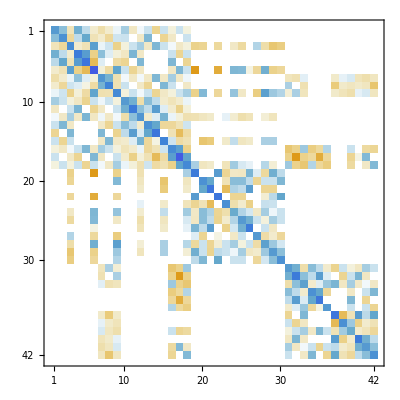

{198.021}

{1.8}

```mathematica
Transpose[𝒮].StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.𝒮//MatrixPlot
```

```mathematica
ee = Transpose[CholeskyDecomposition[Transpose[𝒬].InverseMassSigma.𝒬]];
```

```mathematica
Transpose[𝒬].MassSigma.𝒬//conditionNumber
Inverse[ee].(Transpose[𝒬].MassSigma.𝒬).(Transpose[Inverse[ee]])//conditionNumber
```

```mathematica
Transpose[𝒬].MassSigma.𝒬.Transpose[𝒬].InverseMassSigma.𝒬//conditionNumber
Transpose[𝒬].MassSigma.𝒬.ee.Transpose[ee]//conditionNumber
```

```mathematica
Transpose[𝒬].MassSigma.𝒬
```

```mathematica
bigProduct = Transpose[𝒮].StiffUFromSigma.𝒬.SparseArray[Inverse[Transpose[𝒬].(MassSigma.(𝒬))]].Transpose[𝒬].StiffSigmaFromU.𝒮;
```

```mathematica
conditionNumber[bigProduct]
```

{271.19}

```mathematica
bigProductApprox = Transpose[𝒮].StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.𝒮
```

SparseArray[<900>, {42, 42}]

```mathematica
conditionNumber[bigProductApprox]
```

```mathematica
SparseArray[Inverse[bigProductApprox]].bigProduct.SparseArray[Inverse[bigProductApprox]]//conditionNumber
```

{783.54}

```mathematica
conditionNumber[bigProduct]
```

{17261.2}

```mathematica
α-alpha//Norm
β-beta//Norm
```

6.75819×10^-7

5.94044×10^-6

```mathematica
σ//Length
soln0//Length
```

```mathematica
σ-soln0//Norm
U-soln1//Norm
```

5.94044×10^-6

6.75819×10^-7

5.94043×10^-6

```mathematica
σ = 𝒫.𝓂+𝒬.β;
U=ℛ.ℓ+𝒮.α;
```

```mathematica
Transpose[𝒬].(MassSigma.σ+StiffSigmaFromU.U+F)//Norm
Transpose[𝒮].(StiffUFromSigma.σ+G)//Norm
BoundaryMassForNuePlus.σ-H//Norm
BoundaryMassForDirMinus.U-J//Norm
```

4.76441×10^-10

1.5875×10^-7

0.

8.76559×10^-16

```mathematica
H//Norm
```

0.

```mathematica
β//Norm
beta//Norm
```

1.62504

1.62504

```mathematica
beta - β//Norm
```

2.12261×10^-7

```mathematica
β
```

```mathematica
α//Dimensions
alpha//Dimensions
```

{772}

{772}

```mathematica
α-alpha
```

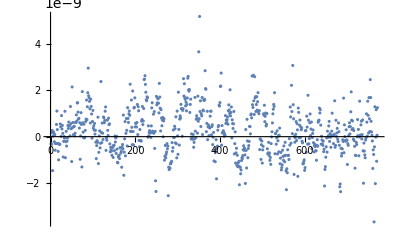

```mathematica
α-alpha//ListPlot
```

```mathematica
rhsSmall = 𝔽-ConjugateTranspose[𝒬].StiffSigmaFromU.𝒮.α;
α-alpha//Norm
β=LinearSolve[Transpose[𝒬].MassSigma.𝒬,rhsSmall];
```

1.35738

```mathematica
α//Norm
alpha//Norm
```

```mathematica
bigProductApprox[x_] := Transpose[𝒮].(StiffUFromSigma.InverseMassSigma.(StiffSigmaFromU.(𝒮.x)));

bigProductPre[x_] := LinearSolve[bigProductApprox,x,Method->{"Krylov",Method->"ConjugateGradient"}]

bigProductPre[x_] := x;
```

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,«1295»,15264},{«1»}},{0.0166667,0.0222222,-0.00555556,0.00833333,0.0111111,-0.00277778,«15252»,0.00277778,-0.0111111,0.00833333,0.00555556,-0.0222222,0.0166667}}] and {0.0215404,-0.0107702,0.0213853,-0.0215404,0.0107702,0.0107702,-0.0646213,«37»,0.000920069,0.154425,-0.154425,-0.463274,0.154485,-0.154485,«1151»} have incompatible shapes.

```mathematica
BoundaryMassForNuePlus.σ-H//Norm

BoundaryMassForNuePlus.(σperp+σpar)-H//Norm

BoundaryMassForNuePlus.(𝒬.β+𝒫.𝓂)-H//Norm

BoundaryMassForNuePlus.(𝒫.𝓂)-H//Norm

Transpose[𝒫].BoundaryMassForNuePlus.(𝒫.𝓂)-Transpose[𝒫].H//Norm

Transpose[𝒫].BoundaryMassForNuePlus.𝒫.𝓂-Transpose[𝒫].H//Norm

PP.SvdΣNuePlus.Transpose[PP].𝓂-Transpose[𝒫].H//Norm

𝓂-LinearSolve[PP.SvdΣNuePlus.Transpose[PP],Transpose[𝒫].H]//Norm
```

0.

0.

0.

«1 more identical outputs»

1.19928×10^-15

1.7856×10^-15

1.46809×10^-14

7.62837×10^-14

```mathematica
BoundaryMassForDirMinus.U-J//Norm
BoundaryMassForDirMinus.(uperp+upar)-J//Norm

BoundaryMassForDirMinus.(𝒮.α+ℛ.ℓ)-J//Norm

BoundaryMassForDirMinus.(ℛ.ℓ)-J//Norm

Transpose[ℛ].BoundaryMassForDirMinus.(ℛ.ℓ)-Transpose[ℛ].J//Norm

Transpose[ℛ].BoundaryMassForDirMinus.ℛ.ℓ-Transpose[ℛ].J//Norm

RR.SvdΣDirMinus.Transpose[RR].ℓ-Transpose[ℛ].J//Norm

ℓ-LinearSolve[RR.SvdΣDirMinus.Transpose[RR],Transpose[ℛ].J]//Norm
```

0.

0.

0.

«1 more identical outputs»

5.9173×10^-16

5.5973×10^-16

5.74983×10^-15

3.90494×10^-13

```mathematica
Transpose[𝒬].(MassSigma.σ+StiffSigmaFromU.U)-𝒬trDotF//Norm
Transpose[𝒮].(-StiffUFromSigma.σ)-𝒮trDotG//Norm


Transpose[𝒬].(MassSigma.(σperp+σpar)+StiffSigmaFromU.(uperp+upar))-𝒬trDotF//Norm
Transpose[𝒮].(-StiffUFromSigma.σ)-𝒮trDotG//Norm


Transpose[𝒬].(MassSigma.(𝒫.𝓂+𝒬.β)+StiffSigmaFromU.(ℛ.ℓ+𝒮.α))-𝒬trDotF//Norm
Transpose[𝒮].(-StiffUFromSigma.(𝒫.𝓂+𝒬.β))-𝒮trDotG//Norm


Transpose[𝒬].MassSigma.(𝒫.𝓂+𝒬.β)+Transpose[𝒬].StiffSigmaFromU.(ℛ.ℓ+𝒮.α)-𝒬trDotF//Norm
-Transpose[𝒮].StiffUFromSigma.(𝒫.𝓂+𝒬.β)-𝒮trDotG//Norm


Transpose[𝒬].MassSigma.𝒬.β+Transpose[𝒬].StiffSigmaFromU.𝒮.α+Transpose[𝒬].MassSigma.𝒫.𝓂+Transpose[𝒬].StiffSigmaFromU.ℛ.ℓ-𝒬trDotF//Norm
-Transpose[𝒮].StiffUFromSigma.𝒬.β-Transpose[𝒮].StiffUFromSigma.𝒫.𝓂-𝒮trDotG//Norm


𝔽=Transpose[𝒬].MassSigma.𝒫.𝓂+Transpose[𝒬].StiffSigmaFromU.ℛ.ℓ-𝒬trDotF;
𝔾=-Transpose[𝒮].StiffUFromSigma.𝒫.𝓂-𝒮trDotG;

Transpose[𝒬].MassSigma.𝒬.β+Transpose[𝒬].StiffSigmaFromU.𝒮.α+𝔽//Norm;
-Transpose[𝒮].StiffUFromSigma.𝒬.β+𝔾//Norm;

QsΣQ[x_] := Transpose[𝒬].(MassSigma.(𝒬.x));

QsΣQPre[x_] := Transpose[𝒬].(InverseMassSigma.(𝒬.x));

QsΣQInv[x_] := LinearSolve[QsΣQ,x,Method->{"Krylov",Method->"ConjugateGradient",Preconditioner->QsΣQPre}]
bigProduct[x_] := Transpose[𝒮].(StiffUFromSigma.(𝒬.QsΣQInv[Transpose[𝒬].(StiffSigmaFromU.(𝒮.x))]))

bigProductApprox[x_] := Transpose[𝒮].(StiffUFromSigma.InverseMassSigma.(StiffSigmaFromU.(𝒮.x)));

bigProductPre[x_] := LinearSolve[bigProductApprox,x,Method->{"Krylov",Method->"ConjugateGradient"}]

bigProductPre[x_] := x;

bigProductInv[x_] := LinearSolve[bigProduct,x,Method->{"Krylov",Method->"ConjugateGradient",Preconditioner->bigProductPre}]


(*𝒬^ᵀ.MassSigma.𝒬.β+𝒬^ᵀ.StiffSigmaFromU.𝒮.α+𝔽//Norm;
-𝒮^ᵀ.StiffUFromSigma.𝒬.β+𝔾//Norm;

ℛ^ᵀ.StiffUFromSigma.𝒬.LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.MassSigma.𝒬.β+𝒬^ᵀ.StiffSigmaFromU.𝒮.α+𝔽]//Norm;

-𝒮^ᵀ.StiffUFromSigma.𝒬.β+𝔾//Norm;

𝒮^ᵀ.StiffUFromSigma.𝒬.(LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.MassSigma.𝒬.β]+LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.StiffSigmaFromU.𝒮.α]+LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝔽])//Norm
-𝒮^ᵀ.StiffUFromSigma.𝒬.β+𝔾//Norm

𝒮^ᵀ.StiffUFromSigma.𝒬.(β+LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.StiffSigmaFromU.𝒮.α]+LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝔽])//Norm
-𝒮^ᵀ.StiffUFromSigma.𝒬.β+𝔾//Norm

𝒮^ᵀ.StiffUFromSigma.𝒬.(β+LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.StiffSigmaFromU.𝒮.α]+LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝔽])-𝒮^ᵀ.StiffUFromSigma.𝒬.β+𝔾//Norm

𝒮^ᵀ.StiffUFromSigma.𝒬.(LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.StiffSigmaFromU.𝒮.α]+LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝔽])+𝔾//Norm

𝒮^ᵀ.StiffUFromSigma.𝒬.(LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.StiffSigmaFromU.𝒮.α]+LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝔽])+𝔾//Norm


(𝒮^ᵀ.StiffUFromSigma.𝒬.LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.StiffSigmaFromU.𝒮.α]+𝒮^ᵀ.StiffUFromSigma.𝒬.LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝔽])+𝔾//Norm

𝒮^ᵀ.StiffUFromSigma.𝒬.Inverse[𝒬^ᵀ.MassSigma.𝒬].𝒬^ᵀ.StiffSigmaFromU.𝒮.α+𝒮^ᵀ.StiffUFromSigma.𝒬.Inverse[𝒬^ᵀ.MassSigma.𝒬].𝔽+𝔾//Norm


(*AAA=𝒮^ᵀ.StiffUFromSigma.𝒬.Inverse[𝒬^ᵀ.MassSigma.𝒬].𝒬^ᵀ.StiffSigmaFromU.𝒮;
BB=𝒮^ᵀ.StiffUFromSigma.𝒬.Inverse[𝒬^ᵀ.MassSigma.𝒬].𝔽+𝔾;
AAA.α+BB//Norm*)


α- (-LinearSolve[AAA,BB])//Norm

𝒬^ᵀ.MassSigma.𝒬.β+𝒬^ᵀ.StiffSigmaFromU.𝒮.α+𝔽//Norm

LinearSolve[𝒬^ᵀ.MassSigma.𝒬,𝒬^ᵀ.StiffSigmaFromU.𝒮.α+𝔽]+β//Norm;*)
```

0.

0.

0.

«3 more identical outputs»

3.24242×10^-16

1.71097×10^-16

1.47793×10^-15

1.31655×10^-15

```mathematica
Transpose[𝒬].MassSigma.𝒬.Transpose[𝒬].InverseMassSigma.𝒬//Normal//Chop//SparseArray//κ
```

1.67572

```mathematica
Transpose[𝒬].MassSigma.𝒬//MatrixPlot
Transpose[𝒬].StiffSigmaFromU.𝒮//MatrixPlot
```

```mathematica
bigProduct[x_] := Transpose[𝒮].(StiffUFromSigma.(𝒬.QsΣQInv[Transpose[𝒬].(StiffSigmaFromU.(𝒮.x))]))
```

```mathematica
Transpose[𝒮].StiffUFromSigma.𝒬.SparseArray[Inverse[Transpose[𝒬].MassSigma.𝒬]].Transpose[𝒬].StiffSigmaFromU.𝒮//MatrixPlot
```

```mathematica
big=-StiffUFromSigma.InverseMassSigma.StiffSigmaFromU;
```

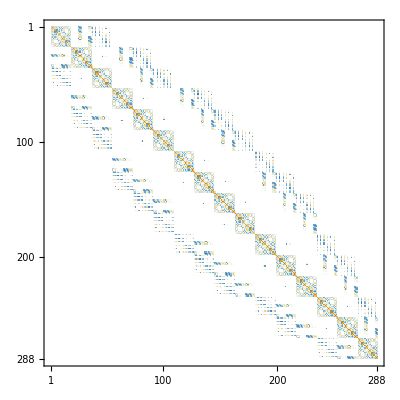

Eigensystem::arh: Because finding 288 out of the 288 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
big//MatrixPlot
{vals,vecs}=Eigensystem[big];
vals=Reverse[vals];
vecs=Reverse[vecs];
```

```mathematica
guess=Plus@@(Transpose[vecs]);
```

```mathematica
ListPlot@Abs[Transpose[vecs].guess]
q=-InverseMassSigma.StiffSigmaFromU.guess;
v=-StiffUFromSigma.q;
(*Δt= Norm[guess]/Norm[v]*)

Δt=-1/2(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v))/((StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v)));


unext=guess+Δt v;
qnext=-InverseMassSigma.StiffSigmaFromU.unext;
vnext=-StiffUFromSigma.qnext;
guess=unext;
```

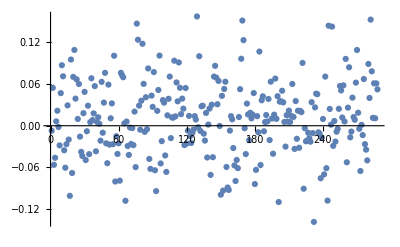

```mathematica
ListPlot@(Transpose[vecs].guess)
guess=MatrixExp[StiffUFromSigma.InverseMassSigma.StiffSigmaFromU,guess];
```

```mathematica
𝒞[i_,j_,k_,l_] := KroneckerDelta[i,k]KroneckerDelta[j,l]+KroneckerDelta[i,l]KroneckerDelta[j,k]+KroneckerDelta[i,j]KroneckerDelta[k,l]
```

```mathematica
∑_(i=1)^3 ∑_(j=1)^3 ∑_(k=1)^3 ∑_(l=1)^3 𝒞[i,j,k,l]σ[i,j]τ[k,l]KroneckerDelta[i,2]KroneckerDelta[j,2]/. {σ[i_,j_] :> σ[j,i]/; i>j,τ[i_,j_] :> τ[j,i]/; i>j}
```

σ[2,2] τ[1,1]+3 σ[2,2] τ[2,2]+σ[2,2] τ[3,3]

```mathematica
Clear[σ]
```

```mathematica
Δt=1
```

```mathematica
(*vnext.vnext//Expand
(StiffUFromSigma.qnext).(StiffUFromSigma.qnext)//Expand*)

(*(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.unext).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.unext)//Expand*)

(*(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess+Δt v)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess+Δt v))//Expand

(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess+Δt 0v)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess+0Δtv))+(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess+0Δt v)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(0guess+Δt v))+(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(0guess+Δt v)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess+0Δt v))+(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(0guess+Δt v)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(0guess+Δt v))//Expand*)


(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess))+2Δt (StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v))+Δt^2(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v))//Expand
```

```mathematica
-(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.(guess)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v))/((StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v)).(StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.( v)))
```

0.338047

```mathematica
Solve[D[568.0821862757842-2689.262781540406 Δt+3977.650742013983 Δt^2,Δt]==0,Δt]
```

{{Δt→0.338047}}

0.356009

```mathematica
Norm[vnext]
```

43.0868

326.756

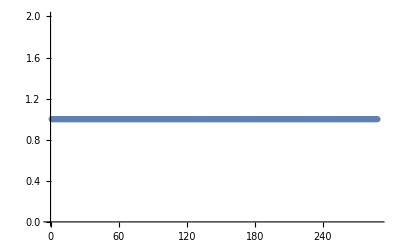

```mathematica
v.guess
```

```mathematica
Δt
```

0.712017

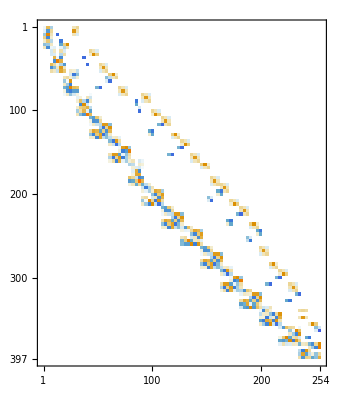

```mathematica
v
```

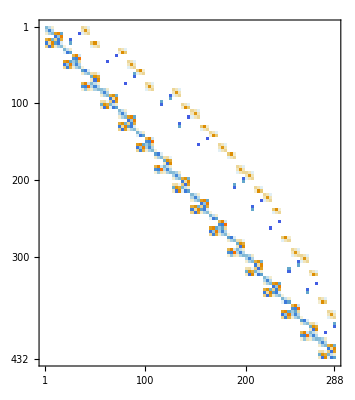

```mathematica
StiffSigmaFromU//MatrixPlot
```

```mathematica
StiffUFromSigma.InverseMassSigma.StiffSigmaFromU//κ
jacob1=SparseArray@DiagonalMatrix[1/#&/@ Normal@Diagonal[StiffUFromSigma.InverseMassSigma.StiffSigmaFromU]]
```

755.912

SparseArray[<288>, {288, 288}]

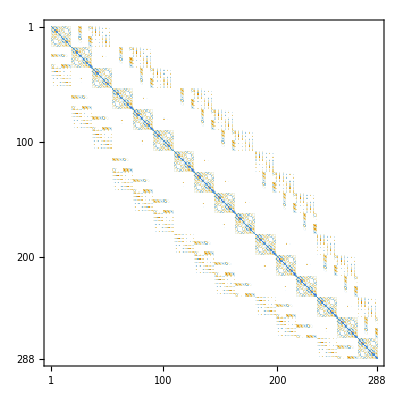

```mathematica
StiffUFromSigma.InverseMassSigma.StiffSigmaFromU//MatrixPlot
```

```mathematica
288/16
```

```mathematica
big=-StiffUFromSigma.InverseMassSigma.StiffSigmaFromU;
```

```mathematica
288/16
```

18

```mathematica
Do[
x=StiffSigmaFromU.(SparseArray@DiagonalMatrix[Table[1,{i,1+18j,18+18j}],0,{288,18}]);
x=SparseArray[x];
block[i,j]=SparseArray@Inverse[Dot[Transpose[x],InverseMassSigma.x]];,
{j,1,16}]
```

```mathematica
precon=SparseArray@ArrayFlatten@
Table[If[i==j,diag[j],0],{i,1,16},{j,1,16}];
```

```mathematica
big//MatrixPlot
```

-Graphics-

```mathematica
16*18
```

288

```mathematica
Clear[block]
Do[
block[i,j]=
big[[1+18(i-1);;18i,1+18(j-1);;18j]],{i,1,16},{j,1,16}]
```

```mathematica
StiffSigmaFromU//MatrixPlot;
s00=StiffSigmaFromU[[1;;432/2,1;;144]]
s01=StiffSigmaFromU[[1;;432/2,145;;-1]]
s10=StiffSigmaFromU[[432/2+1;;-1,1;;144]]
s11=StiffSigmaFromU[[432/2+1;;-1,145;;-1]]
invm00=InverseMassSigma[[1;;432/2,1;;432/2]]
invm11=InverseMassSigma[[432/2+1;;-1,432/2+1;;-1]]
```

SparseArray[<2466>, {216, 144}]

SparseArray[<108>, {216, 144}]

SparseArray[<0>, {216, 144}]

SparseArray[<2466>, {216, 144}]

SparseArray[<3240>, {216, 216}]

SparseArray[<3240>, {216, 216}]

```mathematica
pre=ArrayFlatten[
{{SparseArray@Inverse[Transpose[s00].invm00.s00],0.0},{0.0,
SparseArray@Inverse[Transpose[s01].invm00.s01+Transpose[s11].invm11.s11]}}]
```

SparseArray[<41472>, {288, 288}]

```mathematica
?Eigensystem
```

Eigensystem[m] gives a list {values,vectors} of the eigenvalues and eigenvectors of the square matrix m. 
Eigensystem[{m,a}] gives the generalized eigenvalues and eigenvectors of m with respect to a. 
Eigensystem[m,k] gives the eigenvalues and eigenvectors for the first k eigenvalues of m. 
Eigensystem[{m,a},k] gives the first k generalized eigenvalues and eigenvectors.

```mathematica
{vals,vecs}=Eigensystem[big];
```

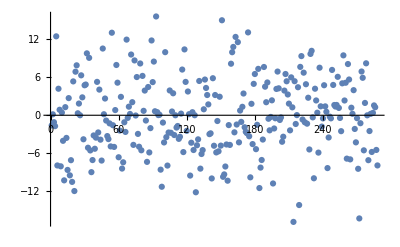

```mathematica
ListPlot[vecs.RandomReal[{-10,10},288],PlotRange->All]
```

```mathematica
Transpose[vecs]
```

Eigensystem::arh: Because finding 288 out of the 288 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
{
```

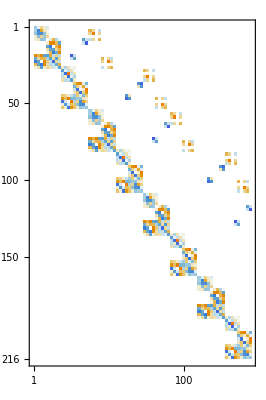

```mathematica
s00//MatrixPlot
```

```mathematica
big.pre//κ
```

242.96

```mathematica
big//κ
```

755.912

```mathematica
Inverse[Transpose[s11].invm11.s11].(Transpose[s01].invm00.s01+Transpose[s11].invm11.s11)//κ
```

86.4511

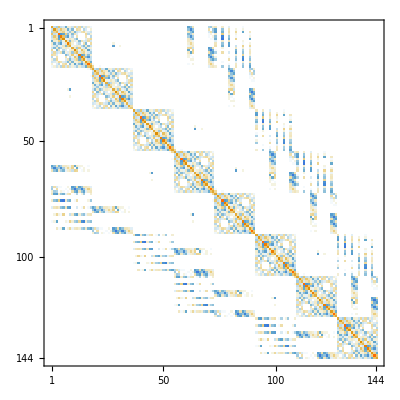

```mathematica
MatrixPlot[Transpose[s01].invm00.s01+Transpose[s11].invm11.s11]
```

```mathematica
ArrayFlatten[
```

-Graphics-

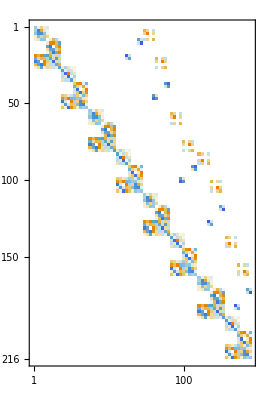

```mathematica
s00//MatrixPlot
s11//MatrixPlot
```

```mathematica
s00
invm00
```

SparseArray[<2466>, {216, 144}]

SparseArray[<3240>, {432, 216}]

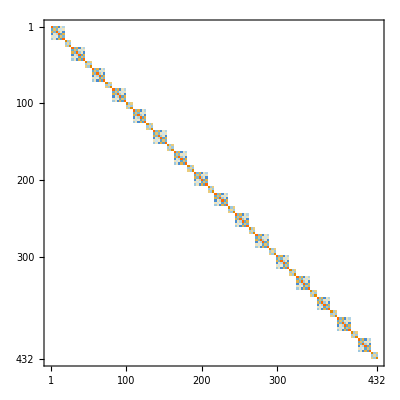

```mathematica
invm00//MatrixPlot
```

```mathematica
InverseMassSigma//MatrixPlot
```

-Graphics-

```mathematica
big//MatrixPlot
```

-Graphics-

```mathematica
Clear[something]
```

```mathematica
L=
ArrayFlatten@Table[
If[j<i,block[i,j],0.0]
,{i,1,16},{j,1,16}]
```

{1}
 |  |  |  |

```mathematica
Transpose[vecs].guess
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
guess=Plus@@(Transpose[vecs]);
```

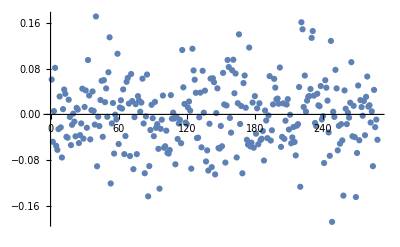

```mathematica
Transpose[vecs].(guess=LinearSolve[ℒ,𝒰.guess])//ListPlot
```

```mathematica
guess
```

```mathematica
𝒩=256;
𝒜=DiagonalMatrix[Table[-2,{i,1,256}]]+DiagonalMatrix[Table[1,{i,1,255}],1]+DiagonalMatrix[Table[1,{i,1,255}],-1];
```

```mathematica
{vals,vecs}=Eigensystem[N[𝒜]];

ℒ=LowerTriangularize[𝒜];
𝒰=𝒜-ℒ;
```

```mathematica
guess=(Plus@@Transpose[(vecs)]);
```

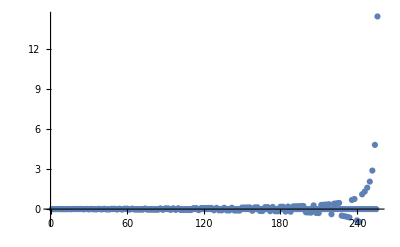

```mathematica
ListPlot[guess,PlotRange->All]
```

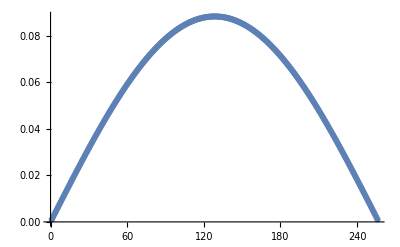

```mathematica
vecs[[-1]]//ListPlot
```

```mathematica
Norm[guess]
```

16.

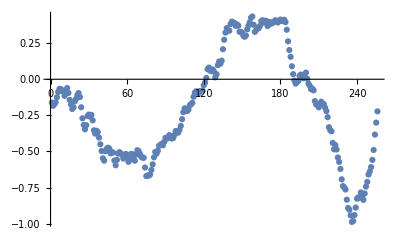

```mathematica
Transpose[vecs].(guess=LinearSolve[ℒ,𝒰.guess])//ListPlot
```

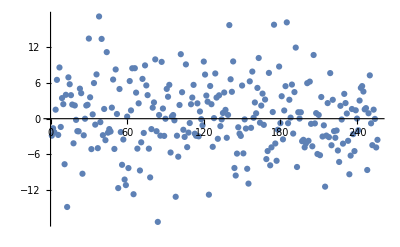

```mathematica
Transpose[vecs].RandomReal[{-10,10},256]//ListPlot
```

```mathematica
256 256
```

65536

```mathematica
vals
```

```mathematica
ℒ=LowerTriangularize[big];
𝒰=big-ℒ;
```

```mathematica
Linea
```

```mathematica
LinearSolve[
```

{{aa,0},{cc,dd}}

```mathematica
L=
ArrayFlatten@Table[
If[j<i,block[i,j],0.0block[i,j]]
,{i,1,16},{j,1,16}]
U=
ArrayFlatten@Table[
If[i<j,block[i,j],0.0block[i,j]]
,{i,1,16},{j,1,16}]
𝒟=
ArrayFlatten@
Table[If[i==j,
block[i,j],0.0block[i,j]],{i,1,16},{j,1,16}]
inv𝒟=
ArrayFlatten@
Table[If[i==j,
block[i,j],0.0block[i,j]],{i,1,16},{j,1,16}]
```

SparseArray[<10692>, {288, 288}]

SparseArray[<10692>, {288, 288}]

SparseArray[<10692>, {288, 288}]

«1 more identical outputs»

```mathematica
LinearSolve[𝒟+L,U]//Eigenvalues;
```

```mathematica
big//MatrixPlot
```

-Graphics-

```mathematica
λ={1,2};
p[x_] := a0+a1 x
```

```mathematica
D[Expand[Sum[(λ[[i]] p[λ⟦i⟧]-1)^2,{i,1,2}]],a1]
```

-10+18 a0+34 a1

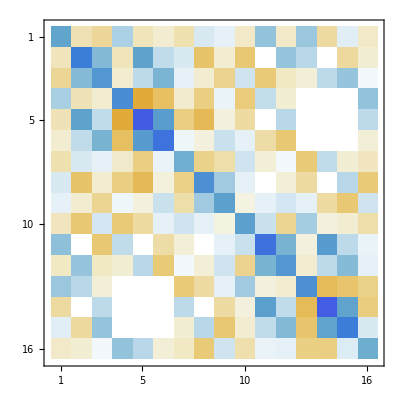

```mathematica
block[1,1]//MatrixPlot
```

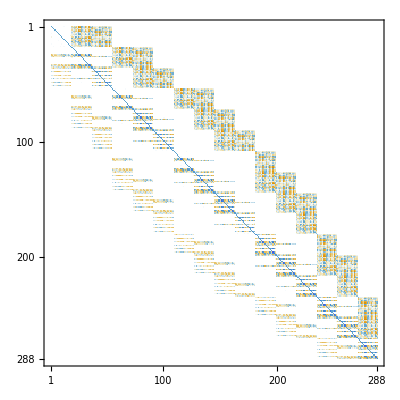

```mathematica
big.precon//MatrixPlot
```

```mathematica
big.precon//κ
```

3531.77

```mathematica
Eigenvalues[-big]
```

Eigenvalues::arh: Because finding 288 out of the 288 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

{4.37872,4.35529,4.35524,4.33727,4.33227,4.29302,4.27593,4.20924,3.99222,3.95619,3.94553,3.938,3.91997,3.90182,3.8586,3.82855,3.57962,3.57955,3.52919,3.51676,3.47042,3.46487,3.36,3.3519,3.19539,3.18502,2.99913,2.95721,2.95576,2.917,2.90661,2.89875,2.80837,2.80765,2.69361,2.6812,2.66372,2.63976,2.62007,2.60509,2.60387,2.58396,2.34858,2.33215,2.31028,2.30528,2.30223,2.29356,2.09207,2.05805,1.89668,1.74511,1.73518,1.68231,1.67808,1.65635,1.64967,1.64538,1.61892,1.60891,1.59262,1.58579,1.58519,1.58358,1.55737,1.53471,1.52846,1.49236,1.48245,1.4719,1.45805,1.4442,1.44364,1.42382,1.4017,1.39673,1.38575,1.35544,1.34496,1.31768,1.29013,1.2881,1.27059,1.26602,1.24853,1.24633,1.2414,1.22139,1.21925,1.20976,1.2054,1.19889,1.18449,1.16875,1.16024,1.13716,1.12799,1.12092,1.11516,1.09932,1.09744,1.07394,1.07137,1.06423,1.05047,1.04205,1.03464,1.01663,1.01428,1.0013,0.988479,0.979819,0.9746,0.962736,0.959872,0.955567,0.935877,0.928621,0.921968,0.921447,0.910976,0.888422,0.868332,0.868091,0.856251,0.84629,0.830975,0.820763,0.818842,0.794315,0.78536,0.766253,0.760353,0.755316,0.747355,0.727487,0.721883,0.712219,0.706258,0.704899,0.700548,0.697814,0.688264,0.684777,0.68179,0.669286,0.659937,0.659216,0.655071,0.650891,0.640276,0.636562,0.628527,0.621475,0.609022,0.596745,0.592677,0.586482,0.580329,0.579058,0.572969,0.554243,0.553144,0.543306,0.542743,0.536278,0.534678,0.52621,0.519477,0.513165,0.509065,0.503906,0.485538,0.483692,0.48138,0.476527,0.470136,0.469047,0.460323,0.455031,0.450784,0.446855,0.438139,0.432511,0.426534,0.424403,0.412987,0.410531,0.409936,0.405956,0.402124,0.396114,0.395379,0.392507,0.389653,0.382297,0.381666,0.380889,0.373173,0.369684,0.363061,0.362386,0.359692,0.358692,0.352854,0.351155,0.347325,0.3424,0.338432,0.333415,0.319177,0.318619,0.31652,0.312668,0.299783,0.298956,0.290535,0.280344,0.276945,0.27418,0.27318,0.266759,0.265852,0.260447,0.259811,0.256699,0.255285,0.240161,0.236806,0.2332,0.228845,0.222754,0.220078,0.21853,0.212887,0.209236,0.198928,0.198763,0.195862,0.186197,0.182973,0.179714,0.175706,0.169659,0.164992,0.160099,0.153713,0.153688,0.150565,0.149545,0.142103,0.139001,0.138888,0.136185,0.131563,0.130541,0.129978,0.126005,0.124776,0.123405,0.123079,0.115637,0.115012,0.110948,0.110341,0.105468,0.105277,0.0999444,0.098748,0.0960471,0.0936454,0.0861977,0.0830388,0.0748626,0.0727249,0.0706135,0.0693934,0.0644554,0.0624962,0.0571325,0.0543159,0.0521025,0.0415451,0.0360858,0.0337511,0.0169863,0.00878859,0.00579264}

```mathematica
Table[1,1

,{i,1,16}]
```

```mathematica
StiffSigmaFromU//MatrixPlot
```

-Graphics-

```mathematica
?Diagonal
```

RowBox[{"Diagonal", "[", StyleBox["m", "TI"], "]"}] gives the list of elements on the leading diagonal of the matrix StyleBox["m", "TI"].
RowBox[{"Diagonal", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives the elements on the StyleBox["k", "TI"]SuperscriptBox["", "th"] diagonal of StyleBox["m", "TI"].

```mathematica
κ[x_] := First@(SingularValueList[x,1]/SingularValueList[x,-1])
```

```mathematica
192/8
```

24

```mathematica
√32
```

4 √2

```mathematica
κ[x_] := First@ (SingularValueList[x,1]/SingularValueList[x,-1])
```

```mathematica
Eigenvalues
```

```mathematica
Eigenvalues@(-StiffUFromSigma.InverseMassSigma.StiffSigmaFromU)//ListPlot[#,PlotRange->All]&
```

Eigenvalues::arh: Because finding 480 out of the 480 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
Eigenvalues@(-StiffUFromSigma.InverseMassSigma.StiffSigmaFromU)
```

Eigenvalues::arh: Because finding 480 out of the 480 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
𝒮//Dimensions
```

{7680,7442}

```mathematica
𝒮.
```

```mathematica
terms=Transpose[𝒬].StiffSigmaFromU.𝒮.SparseArray[
Table[{i+k,j+k}->1,{k,0,3}]/.{i->1,j->1},
{7442,4}];
```

```mathematica
terms
```

SparseArray[<112>, {11281, 4}]

```mathematica
terms
```

SparseArray[<112>, {11281, 4}]

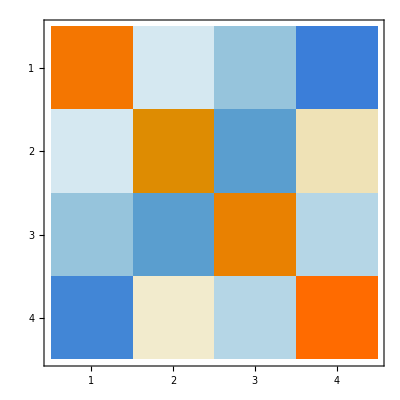

```mathematica
Transpose[terms].Transpose[(SparseArray@Table[QsΣQInv[Normal[terms[[All,i]]]],{i,1,4}])]//MatrixPlot
```

```mathematica
/
```

SparseArray[<16>, {4, 4}]

```mathematica
SparseArray[{i
```

{7680,7442}

```mathematica
big=ArrayFlatten[
{{MassSigma,StiffSigmaFromU},{StiffUFromSigma,0}}
]
```

SparseArray[<2940>, {300, 300}]

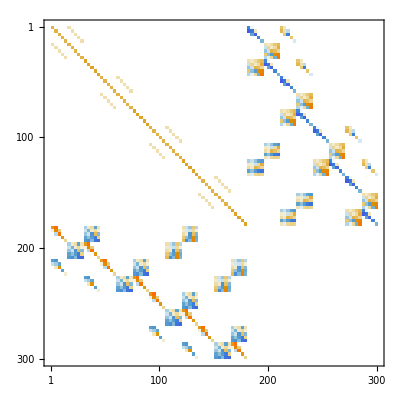

```mathematica
big//MatrixPlot
```

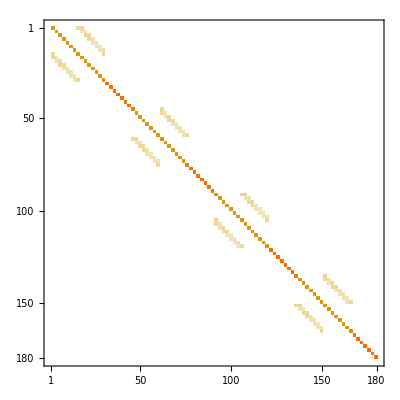

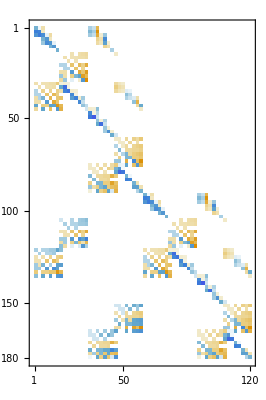

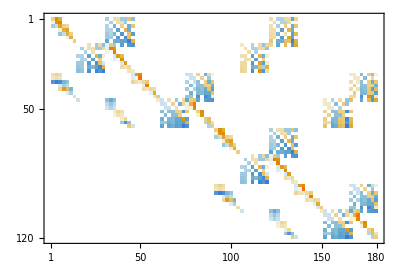

```mathematica
MassSigma//MatrixPlot
StiffSigmaFromU//MatrixPlot
StiffUFromSigma//MatrixPlot
```

```mathematica
Transpose[QQ].QQ//ArrayRules
```

{{1,1}→1,{2,2}→1,{3,3}→1,{4,4}→1,{5,5}→1,{6,6}→1,{7,7}→1,{8,8}→1,{9,9}→1,{10,10}→1,{11,11}→1,{12,12}→1,{13,13}→1,{14,14}→1,{15,15}→1,{16,16}→1,{17,17}→1,{18,18}→1,{19,19}→1,{20,20}→1,{21,21}→1,{22,22}→1,{23,23}→1,{24,24}→1,{25,25}→1,{26,26}→1,{27,27}→1,{28,28}→1,{29,29}→1,{30,30}→1,{31,31}→1,{32,32}→1,{33,33}→1,{34,34}→1,{35,35}→1,{36,36}→1,{37,37}→1,{38,38}→1,{39,39}→1,{40,40}→1,{41,41}→1,{42,42}→1,{43,43}→1,{44,44}→1,{45,45}→1,{65,65}→1,{66,66}→1,{67,67}→1,{68,68}→1,{69,69}→1,{70,70}→1,{71,71}→1,{72,72}→1,{73,73}→1,{74,74}→1,{75,75}→1,{76,76}→1,{77,77}→1,{78,78}→1,{79,79}→1,{80,80}→1,{81,81}→1,{82,82}→1,{83,83}→1,{84,84}→1,{85,85}→1,{86,86}→1,{87,87}→1,{88,88}→1,{89,89}→1,{90,90}→1,{91,91}→1,{92,92}→1,{93,93}→1,{94,94}→1,{95,95}→1,{96,96}→1,{97,97}→1,{98,98}→1,{99,99}→1,{100,100}→1,{101,101}→1,{102,102}→1,{103,103}→1,{104,104}→1,{105,105}→1,{106,106}→1,{107,107}→1,{108,108}→1,{109,109}→1,{110,110}→1,{111,111}→1,{112,112}→1,{113,113}→1,{114,114}→1,{115,115}→1,{116,116}→1,{117,117}→1,{118,118}→1,{119,119}→1,{120,120}→1,{121,121}→1,{122,122}→1,{123,123}→1,{124,124}→1,{125,125}→1,{126,126}→1,{127,127}→1,{128,128}→1,{129,129}→1,{130,130}→1,{131,131}→1,{132,132}→1,{133,133}→1,{134,134}→1,{135,135}→1,{146,146}→1,{147,147}→1,{148,148}→1,{149,149}→1,{150,150}→1,{151,151}→1,{152,152}→1,{153,153}→1,{154,154}→1,{155,155}→1,{156,156}→1,{157,157}→1,{158,158}→1,{159,159}→1,{160,160}→1,{161,161}→1,{162,162}→1,{163,163}→1,{164,164}→1,{165,165}→1,{166,166}→1,{167,167}→1,{168,168}→1,{169,169}→1,{170,170}→1,{171,171}→1,{172,172}→1,{173,173}→1,{174,174}→1,{175,175}→1,{176,176}→1,{177,177}→1,{178,178}→1,{179,179}→1,{180,180}→1,{_,_}→0}

```mathematica
κ[a_] :=First@ (SingularValueList[a,1]/SingularValueList[a,-1])
```

```mathematica
κ[AAA]
```

253.205

```mathematica
κ[AAA.Inverse[Transpose[𝒮].StiffUFromSigma.𝒬.Transpose[𝒬].InverseMassSigma.𝒬.Transpose[𝒬].StiffSigmaFromU.𝒮]]

κ[AAA.Inverse[Transpose[𝒮].StiffUFromSigma.SvdUNeuPlus.Transpose[QQ].Transpose[(SvdUNeuPlus.Transpose[QQ])].InverseMassSigma.(SvdUNeuPlus.Transpose[QQ]).Transpose[(SvdUNeuPlus.Transpose[QQ])].StiffSigmaFromU.𝒮]]
κ[AAA.Inverse[Transpose[𝒮].StiffUFromSigma.InverseMassSigma.StiffSigmaFromU.𝒮]]


κ[AAA.Inverse[Transpose[𝒮].StiffUFromSigma.SvdUNeuPlus.Transpose[QQ].Inverse[QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ]].QQ.Transpose[SvdUNeuPlus].StiffSigmaFromU.𝒮]]
```

```mathematica
κ[AAA.Inverse[Transpose[𝒮].StiffUFromSigma.SvdUNeuPlus.Transpose[QQ].Inverse[QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ]].QQ.Transpose[SvdUNeuPlus].StiffSigmaFromU.𝒮]]
κ[AAA.Inverse[SS.Transpose[SvdUDirMinus].StiffUFromSigma.SvdUNeuPlus.Transpose[QQ].Inverse[QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ]].QQ.Transpose[SvdUNeuPlus].StiffSigmaFromU.SvdUDirMinus.Transpose[SS]]]
```

```mathematica
AAADiagInv=DiagonalMatrix[Map[1/#&,Diagonal[AAA]]];
```

```mathematica
AAA.AAADiagInv//κ
```

1027.84

```mathematica
AAA//κ
```

2602.41

```mathematica
QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ].Inverse[QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ]]//Chop//SparseArray//MatrixPlot
```

```mathematica
Eigenvalues[-AAA]
```

{389.292,376.747,369.266,271.069,250.945,236.438,194.423,172.114,158.81,156.311,139.169,126.329,110.883,101.279,96.4261,84.815,76.0444,68.504,65.4932,65.1352,56.747,53.6542,49.1866,47.3727,46.1763,43.9598,41.5084,39.9238,36.6256,35.3072,32.7478,32.0837,30.8207,30.7101,29.8835,28.4534,27.9796,26.7189,25.9583,25.6997,24.8855,24.0176,23.2579,22.1158,20.2936,19.4978,19.2365,18.8341,18.2029,18.1046,17.2216,16.1082,15.3778,14.9973,14.4066,14.1219,13.8747,13.0784,12.2776,11.761,11.6023,10.9674,10.6168,10.4656,9.74634,9.11471,8.32562,7.7815,7.17763,6.55875,6.51445,6.25258,5.71428,4.64862,4.59809,4.26225,4.07398,3.60405,3.34975,2.81511,2.46864,2.42144,2.36473,1.747,1.56935,0.734169,0.668614,0.63766,0.547006,0.512966,0.324254,0.149589}

```mathematica
QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ].QQ.Inverse[Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus].Transpose[QQ]//Chop//κ
QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ].QQ.Transpose[SvdUNeuPlus].InverseMassSigma.SvdUNeuPlus.Transpose[QQ]//Chop//κ
```

1.125

1.125

```mathematica
MassSigma.Inverse[QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ]]//SparseArray//MatrixPlot
```

Dot::dotsh: Tensors SparseArray[« 1 »] and {{0.375, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., -0.125, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 101 »}, « 49 », « 101 »} have incompatible shapes.

SparseArray::list: List expected at position 1 in SparseArray[TagBox[SparseArray[Automatic, « 2 », {1, {{« 1 »}, « 1 »}, {3.`, 1.`, 3.`, 1.`, 3.`, 0.999999999999999`, 3.`, 0.999999999999999`, 3.`, 1.`, 3.`, 1.`, 3.`, 1.`, 3.`, 0.999999999999999`, 3.`, 0.999999999999999`, « 265 », 3.`, 1.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 3.99999999999999`, 4.`, 4.`, 4.`}}], False, Rule[Editable, False], Rule[SelectWithContents, True]] . « 1 »].

MatrixPlot::mat0: Argument SparseArray[TagBox[SparseArray[Automatic, « 2 », {1, {{« 1 »}, « 1 »}, {3.`, 1.`, 3.`, 1.`, 3.`, 0.999999999999999`, 3.`, 0.999999999999999`, 3.`, 1.`, 3.`, 1.`, 3.`, 1.`, 3.`, 0.999999999999999`, 3.`, 0.999999999999999`, « 265 », 3.`, 1.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 4.`, 3.99999999999999`, 4.`, 4.`, 4.`}}], False, Rule[Editable, False], Rule[SelectWithContents, True]] . « 1 »] at position 1 is not a matrix.

MatrixPlot[SparseArray[SparseArray[<300>, {180, 180}].{1}]]
 |  |  |  |

```mathematica
κ[AAA]
```

2602.41

```mathematica
Inverse[QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ]]
```

```mathematica
StiffUFromSigma.SvdUNeuPlus//Chop//
```

SparseArray[<2344>, {120, 180}]

```mathematica
SvdUNeuPlus.Transpose[QQ].QQ.Transpose[SvdUNeuPlus]//Dimensions
```

{180,180}

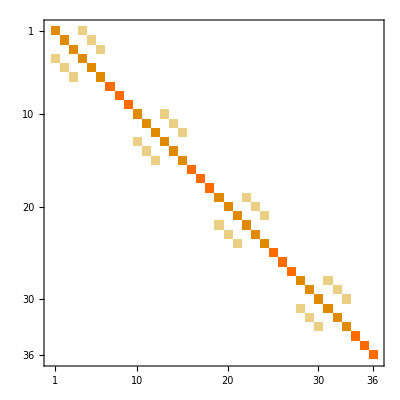

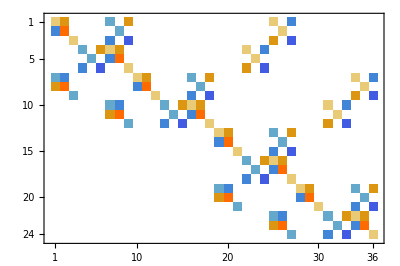

```mathematica
MassSigma//MatrixPlot
StiffUFromSigma//MatrixPlot
```

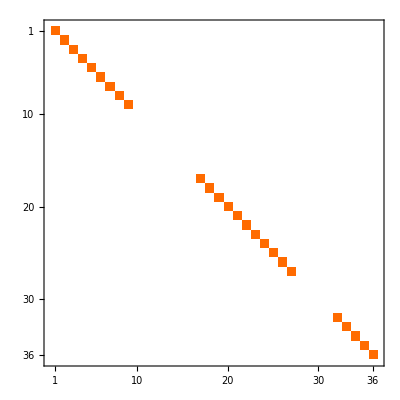

```mathematica
Transpose[QQ].QQ//MatrixPlot
```

```mathematica
𝒬-
```

0

```mathematica
bigProduct[ff]-bigProductApprox[ff]//Norm
```

2.90102

```mathematica
ff=RandomReal[{-1,1},Last@Dimensions@𝒮];
```

```mathematica
bigProductInv[bigProduct[ff]]
```

{0.458842+LinearSolve[bigProduct,Method→{Krylov,Method→ConjugateGradient}],925,-0.22522+LinearSolve[bigProduct,Method→{Krylov,Method→ConjugateGradient}]}
 |  |  |  |

```mathematica
bigProductInv[bigProduct[ff]]-ff//Norm//Timing
```

{0.0235,1.21005×10^-8}

```mathematica
InverseMassSigma
```

```mathematica
2688//FactorInteger
```

```mathematica
8
```

```mathematica
6*8
```

48

```mathematica
2688/48
```

```mathematica
AA=Array[a,{3,3}]/. a[i_,j_] :> a[j,i]/; i>j;
inv1=Tr[AA]
inv2=1/2∑_(i=1)^3 ∑_(j=1)^3 (a[i,i]a[j,j]-a[i,j]a[j,i])/. a[i_,j_] :> a[j,i]/; i>j
inv3=Det[AA];
1/3 ArcCos[(3 inv1^2-9inv1 inv2+27 inv3)/(2(inv1^2-3inv2)^(3/2))]
```

```mathematica
CharacteristicPolynomial[AA,x]
```

-x^3+x^2 a[1,1]+x a[1,2]^2+x a[1,3]^2+x^2 a[2,2]-x a[1,1] a[2,2]-a[1,3]^2 a[2,2]+2 a[1,2] a[1,3] a[2,3]+x a[2,3]^2-a[1,1] a[2,3]^2+x^2 a[3,3]-x a[1,1] a[3,3]-a[1,2]^2 a[3,3]-x a[2,2] a[3,3]+a[1,1] a[2,2] a[3,3]

```mathematica
Eigenvalues[AA]
```

{Root[a[1,3]^2 a[2,2]-2 a[1,2] a[1,3] a[2,3]+a[1,1] a[2,3]^2+a[1,2]^2 a[3,3]-a[1,1] a[2,2] a[3,3]+(-a[1,2]^2-a[1,3]^2+a[1,1] a[2,2]-a[2,3]^2+a[1,1] a[3,3]+a[2,2] a[3,3]) #1+(-a[1,1]-a[2,2]-a[3,3]) #1^2+#1^3&,1],Root[a[1,3]^2 a[2,2]-2 a[1,2] a[1,3] a[2,3]+a[1,1] a[2,3]^2+a[1,2]^2 a[3,3]-a[1,1] a[2,2] a[3,3]+(-a[1,2]^2-a[1,3]^2+a[1,1] a[2,2]-a[2,3]^2+a[1,1] a[3,3]+a[2,2] a[3,3]) #1+(-a[1,1]-a[2,2]-a[3,3]) #1^2+#1^3&,2],Root[a[1,3]^2 a[2,2]-2 a[1,2] a[1,3] a[2,3]+a[1,1] a[2,3]^2+a[1,2]^2 a[3,3]-a[1,1] a[2,2] a[3,3]+(-a[1,2]^2-a[1,3]^2+a[1,1] a[2,2]-a[2,3]^2+a[1,1] a[3,3]+a[2,2] a[3,3]) #1+(-a[1,1]-a[2,2]-a[3,3]) #1^2+#1^3&,3]}

```mathematica
1/2(inv1^2-Tr[AA.AA])
```

0

-a[1,3]^2 a[2,2]+2 a[1,2] a[1,3] a[2,3]-a[1,1] a[2,3]^2-a[1,2]^2 a[3,3]+a[1,1] a[2,2] a[3,3]

```mathematica
Collect[Det[AA-λ IdentityMatrix[3]],λ]
```

-λ^3-a[1,3]^2 a[2,2]+2 a[1,2] a[1,3] a[2,3]-a[1,1] a[2,3]^2-a[1,2]^2 a[3,3]+a[1,1] a[2,2] a[3,3]+λ^2 (a[1,1]+a[2,2]+a[3,3])+λ (a[1,2]^2+a[1,3]^2-a[1,1] a[2,2]+a[2,3]^2-a[1,1] a[3,3]-a[2,2] a[3,3])

```mathematica
∑_(i=0)^pp ∑_(j=0)^(pp-i) ∑_(k=0)^(pp-i-j) 1//Factor
```

1/6 (1+pp) (2+pp) (3+pp)

```mathematica
?LinearSolve
```

RowBox[{"LinearSolve", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["b", "TI"]}], "]"}] finds an StyleBox["x", "TI"] that solves the matrix equation RowBox[{RowBox[{StyleBox["m", "TI"], ".", StyleBox["x", "TI"]}], "==", StyleBox["b", "TI"]}]. 
RowBox[{"LinearSolve", "[", StyleBox["m", "TI"], "]"}] generates a RowBox[{"LinearSolveFunction", "[", StyleBox["…", "TR"], "]"}] that can be applied repeatedly to different StyleBox["b", "TI"].

```mathematica
ArrayFlatten[
{{Transpose[𝒬].MassSigma.𝒬,Transpose[𝒬].StiffSigmaFromU.𝒮},{-Transpose[𝒮].StiffUFromSigma.𝒬,0} }
]
```

```mathematica
AA11=Transpose[𝒬].MassSigma.𝒬;
AA12=Transpose[𝒬].StiffSigmaFromU.𝒮;
AA21=Transpose[𝒮].StiffUFromSigma.𝒬;
```

```mathematica
ArrayFlatten[{{AA11,AA12},{AA21,0}}]
```

$Aborted

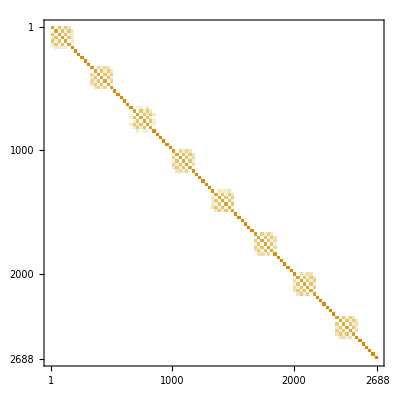

```mathematica
MassSigma//MatrixPlot
```

```mathematica
AAA//SingularValueList
AAA.Inverse[Transpose[𝒮].StiffUFromSigma.𝒬.Transpose[𝒬].InverseMassSigma.𝒬.Transpose[𝒬].StiffSigmaFromU.𝒮]//SingularValueList
```

{800.582,782.05,765.274,560.877,524.133,520.239,430.124,399.707,378.525,355.165,335.446,290.163,257.842,239.977,211.517,204.892,193.216,184.451,163.966,157.213,140.84,132.613,129.745,121.109,114.033,100.065,97.1306,96.9832,94.11,90.1646,87.0763,83.5355,72.8205,70.8762,66.7331,64.6766,63.2862,61.7604,61.15,58.6155,56.7794,56.2222,55.5313,53.9725,52.3725,48.6927,47.8461,47.4518,45.373,44.6471,43.8049,43.6047,42.2526,40.8597,40.2518,39.6182,38.9258,36.938,35.5995,34.8164,34.0913,33.1636,32.054,31.6022,30.6472,29.8776,28.7413,28.3311,27.7182,27.35,26.5172,25.6621,25.1789,24.9637,24.1954,23.5862,23.2188,22.357,22.0315,21.6427,21.052,20.5744,20.5091,19.4414,19.2541,19.1385,18.3804,17.7745,17.3859,16.8092,16.6519,16.1124,15.1813,14.7969,14.3928,14.2038,13.0803,12.6212,12.4342,11.9901,11.7183,10.5841,10.2704,10.093,9.64613,9.02525,8.42455,7.69518,7.60387,7.25136,6.78358,6.44438,5.99418,5.9185,5.4938,4.68292,4.29873,4.19545,3.88203,3.37178,3.25841,3.20461,2.98226,2.44103,2.40677,1.77482,1.60847,0.734532,0.668554,0.650804,0.6159,0.589183,0.327267,0.15438}

{1.17383,1.07052,1.04732,1.03741,1.02444,1.02232,1.01904,1.0117,1.00821,1.007,1.00547,1.00402,1.00208,1.00151,1.00127,1.00037,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.961622,0.94899,0.941833,0.936241,0.916441,0.911564,0.908935,0.902529,0.897273,0.89137,0.885807,0.876349,0.862676,0.850194,0.8351,0.784928}

```mathematica
Transpose[𝒮].StiffUFromSigma.𝒬.Transpose[𝒬].InverseMassSigma.𝒬.Transpose[𝒬].StiffSigmaFromU.𝒮//SingularValueList
```

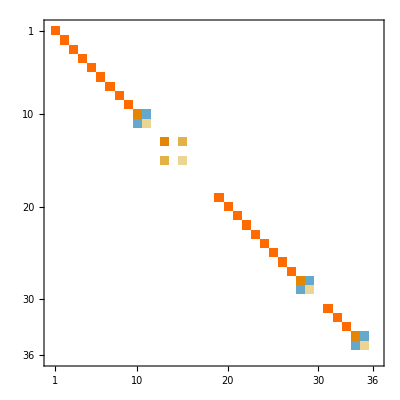

```mathematica
𝒬.Transpose[𝒬]//MatrixPlot
```

```mathematica
SingularValuesList[Transpose[𝒮].StiffUFromSigma.𝒬.Transpose[𝒬].InverseMassSigma.𝒬.Transpose[𝒬]
```

```mathematica
LinearSolve[
```

{1.05725,1.02116,1.00225,1.00149,1.,1.,1.,1.,1.,1.,0.961261,0.926339,0.902665,0.855722}

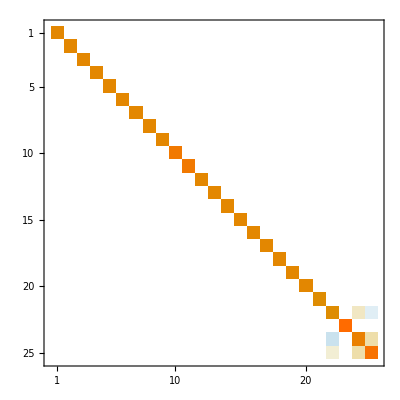

```mathematica
Transpose[𝒬].MassSigma.𝒬.(Transpose[𝒬].InverseMassSigma.𝒬)//Chop//ArrayRules;
QQ.Transpose[SvdUNeuPlus].MassSigma.SvdUNeuPlus.Transpose[QQ]//MatrixPlot;
Transpose[𝒬].InverseMassSigma.𝒬.(Transpose[𝒬].MassSigma.𝒬)//MatrixPlot
```

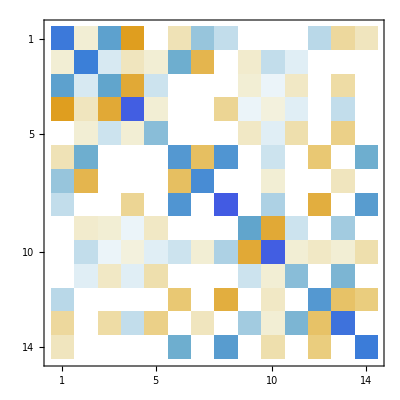

```mathematica
Transpose[𝒮].StiffUFromSigma.𝒬.Transpose[𝒬].InverseMassSigma.𝒬.Transpose[𝒬].StiffSigmaFromU.𝒮//Chop//MatrixPlot
```

```mathematica
Transpose[QQ].QQ//MatrixPlot
```

-Graphics-

```mathematica
AAA//SingularValueList
```

```mathematica
AAA//Dimensions
```

{10,14}

0.

0.

0.

«3 more identical outputs»

1.42109×10^-14

5.16463×10^-15

1.67816×10^-14

5.16463×10^-15

2.2835×10^-14

5.16463×10^-15

2.2835×10^-14

5.16463×10^-15

```mathematica
σperp+σpar
```

{5.24322,-7.05988,5.58605,4.4399,-8.98394,0.260339,-2.17196,0.722482,4.56846,10.4089,-0.0740529,-7.22372,3.65586,-7.63,11.1756,-4.29531,-10.6683,-1.00086,8.28923,6.1199,0.120605,-2.62095,7.91417,2.55114,-0.370969,1.54771,0.90791,4.6013,-7.55477,-7.1309,3.26433,1.50023,2.05088,2.16936,4.17811,7.23663}

```mathematica
uperp+upar
```

{7.69242,3.33515,5.08464,8.63962,-5.57736,-5.11866,-5.34537,1.66551,-7.39261,7.05806,0.637315,8.04745,-1.85202,-4.34796,8.13028,10.1722,-4.9757,-4.70645,-6.77145,6.80072,-8.67215,6.75795,-4.57769,4.78182}

```mathematica
σperp//
```

{5.24322,-7.05988,5.58605,4.4399,-8.98394,0.260339,-2.17196,0.722482,4.56846,7.83874,-4.5257,0.,7.58107,0.,4.37693,0.,0.,0.,8.28923,6.1199,0.120605,-2.62095,7.91417,2.55114,-0.370969,1.54771,0.90791,6.72229,-3.88112,0.,3.26433,1.50023,2.05088,-0.18215,0.105165,0.}

```mathematica
𝒮.α
σpar
```

{7.21348,4.16471,0.,4.06464,2.34672,0.,-5.34537,1.66551,-7.39261,7.05806,0.637315,8.04745,0.,0.,0.,0.,0.,0.,-6.77145,6.80072,-8.67215,6.75795,-4.57769,4.78182}

SparseArray[<11>, {11, 11}]

{0.,0.,0.,0.,0.,0.,0.,0.,0.,-12.2828,-21.2744,-0.749058,-2.10059,-9.42801,3.63833,0.473846,-14.9769,-22.9153,0.,0.,0.,0.,0.,0.,0.,0.,0.,-6.75764,-11.7046,-1.68759,0.,0.,0.,-7.72957,-13.388,7.64572}

```mathematica
Transpose[𝒫].BoundaryMassForNuePlus.𝒫//Chop//Normal//Diagonal
Transpose[PP].SvdΣNuePlus.PP//Normal//Diagonal
```

{5.64575,4.,4.,4.,1.,1.,0.354249,4.,4.,1.,1.}

{5.64575,4.,4.,4.,1.,1.,0.354249,4.,4.,1.,1.}

```mathematica
SingularValueList[BoundaryMassForNuePlus]
```

{5.64575,4.,4.,4.,4.,4.,1.,1.,1.,1.,0.354249}

```mathematica
BoundaryMassForNuePlus.SvdUNeuPlus.QQ//Chop//MatrixPlot
```

-Graphics-

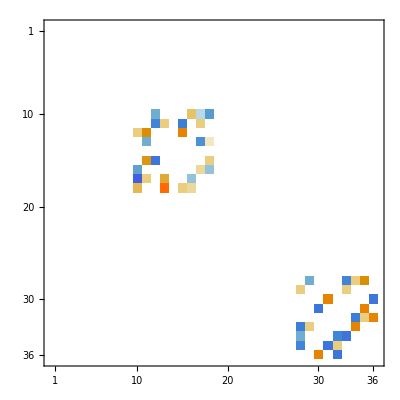

```mathematica
SvdUNeuPlus-SvdVtNeuPlus//Chop//MatrixPlot
```

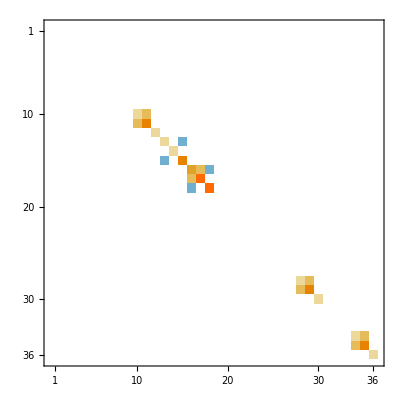

```mathematica
BoundaryMassForNuePlus//MatrixPlot
```

-Graphics-

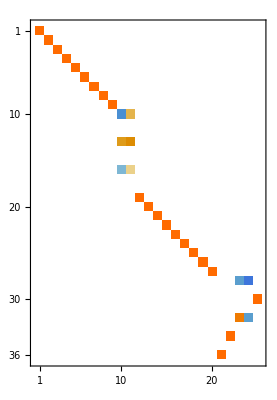

```mathematica
BoundaryMassForNuePlus-SvdUNeuPlus.SvdΣNuePlus.SvdVtNeuPlus//Normal//Chop//MatrixPlot


SvdVtNeuPlus.QQ//Normal//Chop//MatrixPlot
```

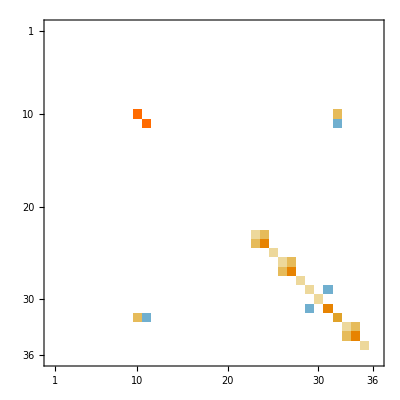

```mathematica
ArrayFlatten[
{{Transpose[QQ].BoundaryMassForNuePlus.QQ,Transpose[QQ].BoundaryMassForNuePlus.PP},{Transpose[PP].BoundaryMassForNuePlus.QQ,Transpose[PP].BoundaryMassForNuePlus.PP}}]//MatrixPlot
```

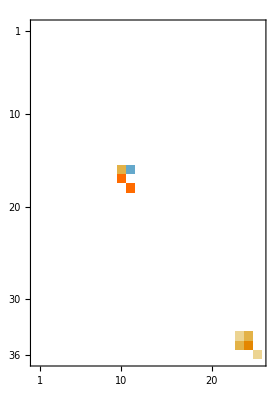

```mathematica
.QQ//MatrixPlot
```

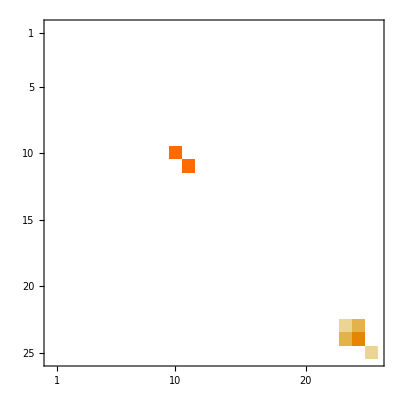

```mathematica
Transpose[QQ].BoundaryMassForNuePlus.QQ//MatrixPlot
```

```mathematica
Transpose[PP].
```

```mathematica
σ
```

{-8.10078,-7.52832,7.32753,-9.82994,8.14057,4.71416,8.73739,-9.1118,-6.20661,5.86307,-3.15269,-8.77281,-8.17182,1.90014,5.44753,7.52174,7.97886,-2.47096,5.01014,6.87559,0.225939,-3.28797,2.65383,-3.26644,-4.47209,-2.59745,-4.74523,2.27165,1.21811,-3.7489,-6.43767,0.247778,3.75491,7.97188,-4.36344,2.29018}

```mathematica
PP//Dimensions
QQ//Dimensions
```

{36,11}

{36,25}

```mathematica
RR.ℓ
SS.α
```

```mathematica
RR//Dimensions
SS//Dimensions
```

{10,24}

{14,24}

```mathematica
Length[RR]
```

10

SparseArray[<14>, {14, 24}]

```mathematica
BoundaryMassForNuePlus.Transpose[(QQ.Vtn)]//Normal//Chop//Norm
BoundaryMassForDirMinus.Transpose[(SS.Vtd)]//Normal//Chop//Norm
```

0

```mathematica
BoundaryMassForNuePlus.
```

0

```mathematica
?Position
```

RowBox[{"Position", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"]}], "]"}] gives a list of the positions at which objects matching StyleBox["pattern", "TI"] appear in StyleBox["expr", "TI"]. 
RowBox[{"Position", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] finds only objects that appear on levels specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Position", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the positions of the first StyleBox["n", "TI"] objects found. 
RowBox[{"Position", "[", StyleBox["pattern", "TI"], "]"}] represents an operator form of Position that can be applied to an expression.

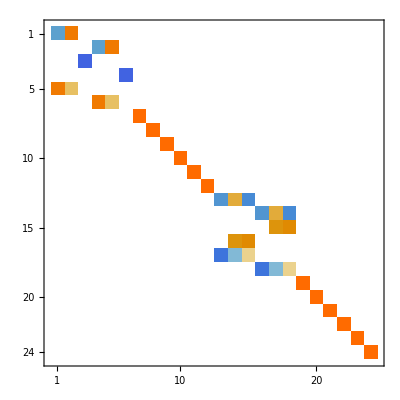

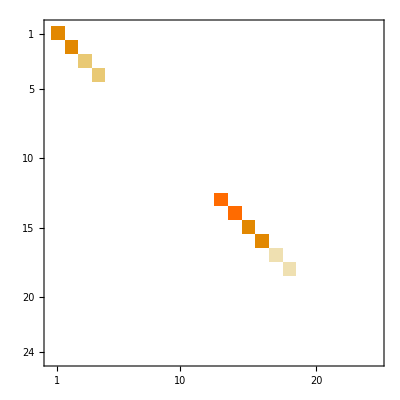

```mathematica
Vtd//MatrixPlot
Σd//MatrixPlot
```

```mathematica
Ud.Σd.Vtd-BoundaryMassForDirMinus//Chop//MatrixPlot
Un.Σn.Vtn-BoundaryMassForNuePlus//Chop//MatrixPlot
```

-Graphics-

-Graphics-

```mathematica
Ud
```

```mathematica
σ=RandomReal[{-10,10},Length[MassSigma]];
U=RandomReal[{-10,10},Length[StiffUFromSigma]];
F=MassSigma.σ+StiffSigmaFromU.U
G=-StiffUFromSigma.σ
```

```mathematica
Ud
```

```mathematica
W=NullSpace[BoundaryMassForNuePlus];
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
?.
```

a.b.c or Dot[a,b,c] gives products of vectors, matrices, and tensors.

```mathematica
U//Length
σ//Length
```

8192

12288

```mathematica
?U
```

Global`U

U={{-0.382867,0.,0.,0.,1.63369×10^-16,0.,0.,-0.196108,0.,0.,0.,0.,-1.68341×10^-16,0.,0.,-0.502449},{0.410449,0.,0.,0.,0.433013,0.,0.,-0.0899542,0.,0.,0.,0.,-0.559017,0.,0.,0.3687},{-0.470009,0.,0.,0.,-0.559017,0.,0.,-0.260266,0.,0.,0.,0.,-0.433013,0.,0.,0.459731},{0.410449,0.,0.,0.,-0.433013,0.,0.,-0.0899542,0.,0.,0.,0.,0.559017,0.,0.,0.3687},{-0.273237,0.,0.,0.,-8.88178×10^-16,0.,0.,0.899934,0.,0.,0.,0.,4.38885×10^-16,0.,0.,0.230131},{-0.470009,0.,0.,0.,0.559017,0.,0.,-0.260266,0.,0.,0.,0.,0.433013,0.,0.,0.459731},{0.,-0.382867,0.,0.,0.,1.63369×10^-16,-0.196108,0.,0.,0.,0.,0.,0.,-1.68341×10^-16,-0.502449,0.},{0.,0.410449,0.,0.,0.,0.433013,-0.0899542,0.,0.,0.,0.,0.,0.,-0.559017,0.3687,0.},{0.,-0.470009,0.,0.,0.,-0.559017,-0.260266,0.,0.,0.,0.,0.,0.,-0.433013,0.459731,0.},{0.,0.410449,0.,0.,0.,-0.433013,-0.0899542,0.,0.,0.,0.,0.,0.,0.559017,0.3687,0.},{0.,-0.273237,0.,0.,0.,-8.88178×10^-16,0.899934,0.,0.,0.,0.,0.,0.,4.38885×10^-16,0.230131,0.},{0.,-0.470009,0.,0.,0.,0.559017,-0.260266,0.,0.,0.,0.,0.,0.,0.433013,0.459731,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.57735,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.745356,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-0.5,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.866025,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.57735,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.745356,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.5,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.866025,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

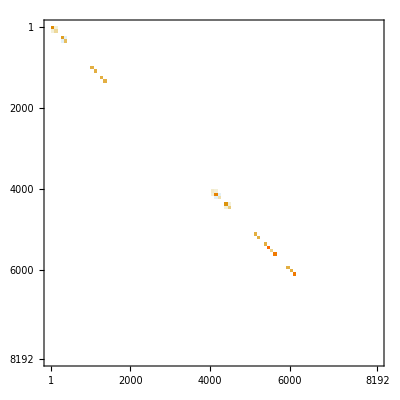

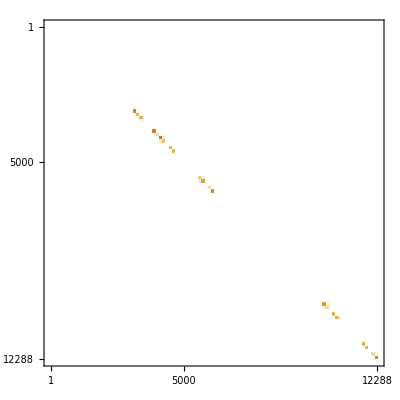

```mathematica
BoundaryMassForDirMinus//MatrixPlot
BoundaryMassForNuePlus//MatrixPlot
```

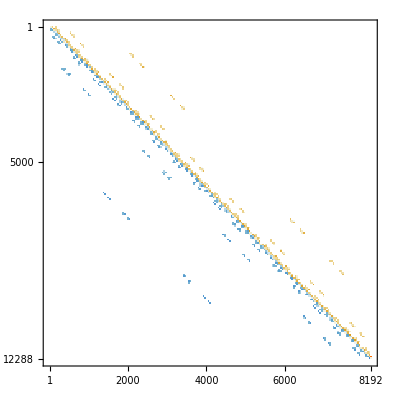

```mathematica
StiffSigmaFromU//MatrixPlot
```

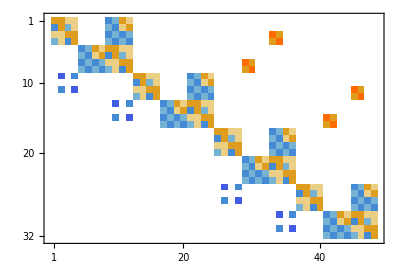

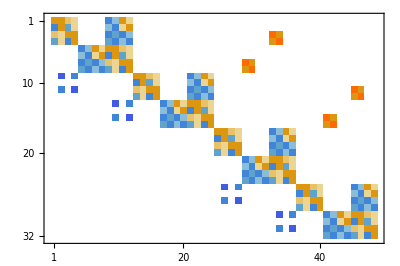

```mathematica
OLDStiffUFromSigma//MatrixPlot
StiffUFromSigma//MatrixPlot
```

```mathematica
(StiffUFromSigma//ByteCount)/(1024 1024)//N
```

3.79763

```mathematica
OLDStiffUFromSigma-   StiffUFromSigma//Normal//Chop//MatrixPlot
 OLDStiffSigmaFromU-
StiffSigmaFromU//Normal//Flatten//Union
```

-Graphics-

{-9.71445×10^-17,0.,9.71445×10^-17}

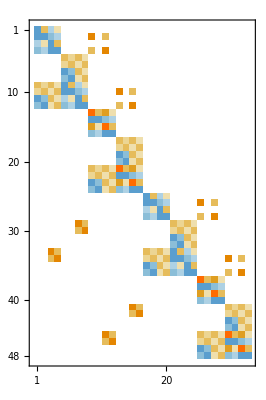

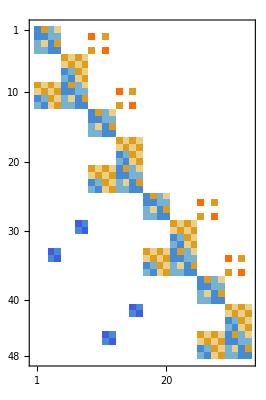

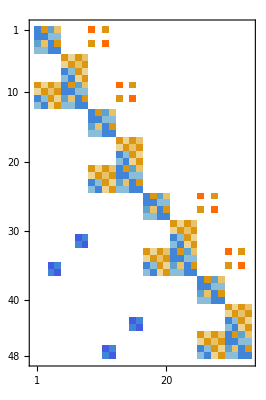

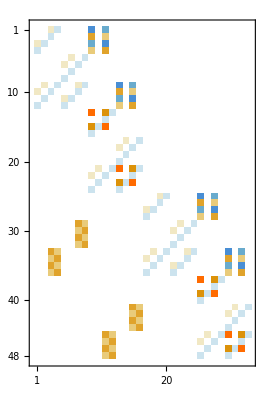

```mathematica
StiffSigmaFromU//MatrixPlot
OLDStiffSigmaFromU//MatrixPlot
-Transpose[StiffUFromSigma]//MatrixPlot
  StiffSigmaFromU- (-  Transpose[StiffUFromSigma])//Normal//MatrixPlot
```

```mathematica
fff=
```

```mathematica
?Import
```

RowBox[{"Import", "[", StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] imports data from a file, returning a complete StyleBox["Wolfram Language", "RebrandingTerm"] version of it. 
RowBox[{"Import", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["elements", "TI"]}], "]"}] imports the specified elements from a file.
RowBox[{"Import", "[", RowBox[{StyleBox["\"http://\!\(\*StyleBox[\"url\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] and RowBox[{"Import", "[", RowBox[{StyleBox["\"ftp://\!\(\*StyleBox[\"url\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] imports from any accessible URL.

```mathematica
{U,Σ,V}=SingularValueDecomposition[Normal[BB],rank];
```

```mathematica
U//Dimensions
Σ//Dimensions
V//Dimensions
```

{{3.10862×10^-15,1.77636×10^-15,4.44089×10^-16,1.9984×10^-15,1.80411×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{4.21885×10^-15,-1.33227×10^-15,2.22045×10^-15,6.05765×10^-15,-3.77476×10^-15,-4.1217×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.77636×10^-15,1.77636×10^-15,-2.66454×10^-15,-2.96985×10^-15,2.80331×10^-15,2.45637×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.33227×10^-15,2.29677×10^-15,-4.70457×10^-15,-3.10862×10^-15,1.55431×10^-15,1.77636×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-2.01228×10^-16,2.22045×10^-15,-1.42941×10^-15,-4.44089×10^-16,5.32907×10^-15,-9.22873×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{3.10862×10^-15,-1.72085×10^-15,2.96985×10^-15,1.33227×10^-15,-4.23273×10^-15,8.88178×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,3.10862×10^-15,1.9984×10^-15,4.44089×10^-16,1.77636×10^-15,-4.16334×10^-17,4.44089×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,3.9968×10^-15,-1.77636×10^-15,2.22045×10^-15,7.26502×10^-15,-3.77476×10^-15,-5.64826×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-1.77636×10^-15,2.66454×10^-15,-2.66454×10^-15,-2.81719×10^-15,2.76862×10^-15,2.38698×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-1.33227×10^-15,1.96371×10^-15,-4.8711×10^-15,-2.66454×10^-15,1.77636×10^-15,1.77636×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-2.08167×10^-16,1.11022×10^-15,-7.56339×10^-16,-4.44089×10^-16,6.21725×10^-15,-6.8695×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,3.55271×10^-15,-4.02456×10^-16,2.34535×10^-15,0.,-5.10703×10^-15,1.77636×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.77636×10^-15,1.11022×10^-15,1.33227×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-6.66134×10^-16,3.55271×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.9968×10^-15,-8.88178×10^-16,3.55271×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.22045×10^-15,6.66134×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.44089×10^-16,1.33227×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.77636×10^-15,1.11022×10^-15,1.33227×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-6.66134×10^-16,3.55271×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.9968×10^-15,-8.88178×10^-16,3.55271×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.22045×10^-15,6.66134×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.44089×10^-16,1.33227×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
Transpose[U].U//Chop
Σ
V
```

```mathematica
rank=Length@SingularValueList[Normal[BB]];
{vals,vecs}=Eigensystem[BB,rank];
```

```mathematica
Transpose[vecs].DiagonalMatrix[vals].vecs-BB
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

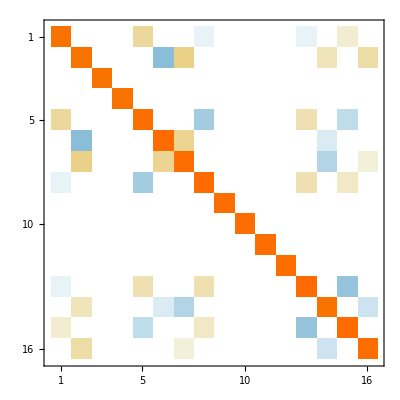

```mathematica
vecs.Transpose[vecs]//MatrixPlot
```

```mathematica
SingularValueList[Normal[BB]]
```

{11.2037,11.2037,9.,9.,9.,9.,6.34626,6.34626,4.,4.,1.,1.,1.,1.,0.450061,0.450061}

```mathematica
(Transpose[U])[[1;;rank]].U.Σ.Transpose[V]//MatrixPlot
```

```mathematica
(Transpose[U])[[1;;rank]].U.Σ.Transpose[V]//Dimensions
```

{16,48}

```mathematica
V//Dimensions
```

{48,48}

```mathematica
Σ.Transpose[V]//Dimensions
```

{48,48}

```mathematica
?SingularValueDecomposition
```

SingularValueDecomposition[m] gives the singular value decomposition for a numerical matrix m as a list of matrices {u,w,v}, where w is a diagonal matrix and m can be written as u.w.Conjugate[Transpose[v]]. 
SingularValueDecomposition[{m,a}] gives the generalized singular value decomposition of m with respect to a. 
SingularValueDecomposition[m,k] gives the singular value decomposition associated with the k largest singular values of m. 
SingularValueDecomposition[{m,a},k] gives the generalized singular value decomposition associated with the k largest singular values.

```mathematica
U//Dimensions
Σ//Dimensions
V//Dimensions
```

{48,48}

{48,48}

{48,48}

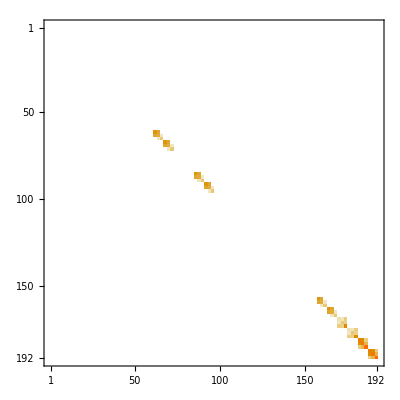

```mathematica
AA//MatrixPlot
```

```mathematica
Σ//Diagonal
```

{11.2037,11.2037,9.,9.,9.,9.,6.34626,6.34626,4.,4.,1.,1.,1.,1.,0.450061,0.450061,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
{vals,vecs}=Eigensystem[(Normal[AA]+Transpose[Normal[AA]])/2];
vecs.AA.Transpose[vecs]//Chop//MatrixPlot
```

```mathematica
Σ//Diagonal
```

{11.2037,11.2037,9.,9.,9.,9.,6.34626,6.34626,4.,4.,1.,1.,1.,1.,0.450061,0.450061,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

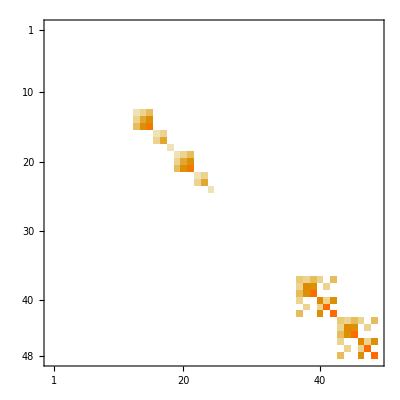

```mathematica
AA//MatrixPlot
```

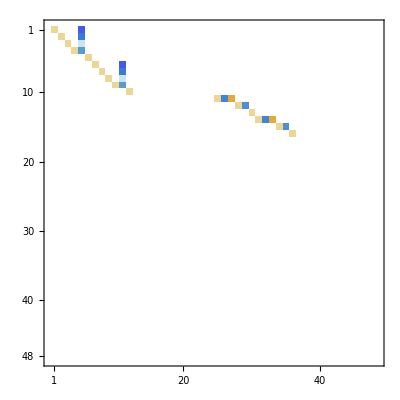

```mathematica
RowReduce[BB]//MatrixPlot
```

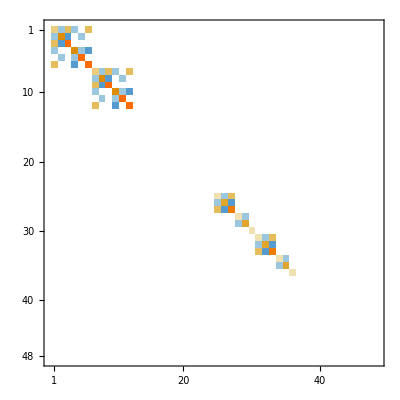

```mathematica
BB//MatrixPlot
```

```mathematica
vals
```

{11.2037,11.2037,9.,9.,9.,9.,6.34626,6.34626,4.,4.,1.,1.,1.,1.,0.450061,0.450061,-4.77396×10^-15,-4.77396×10^-15,3.55271×10^-15,3.55271×10^-15,-2.44249×10^-15,-2.44249×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

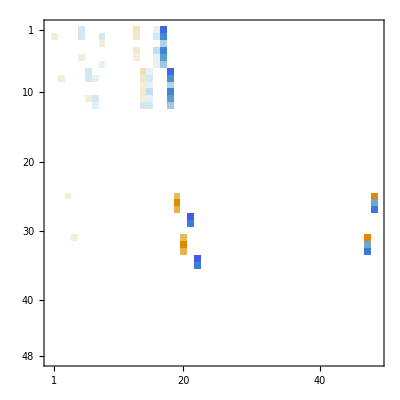

```mathematica
U-V//MatrixPlot
```

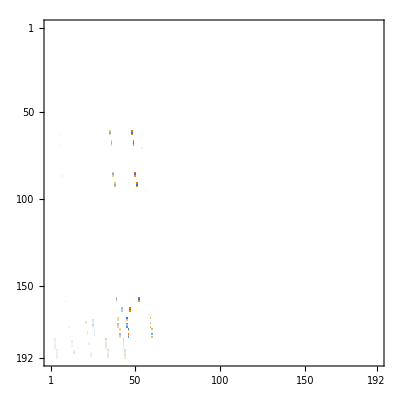

```mathematica
U-V//M
```

```mathematica
AA-Transpose[AA]
```

0.

```mathematica
U.Σ.Transpose[V]-AA
```

7.74984×10^-15

```mathematica
Normal
```

-Graphics-

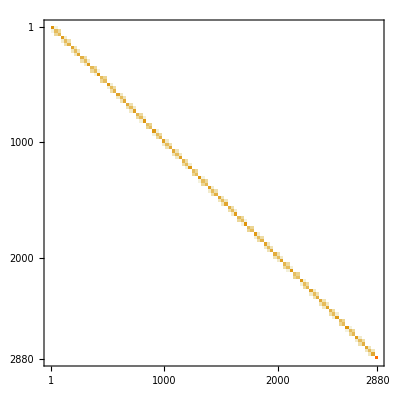

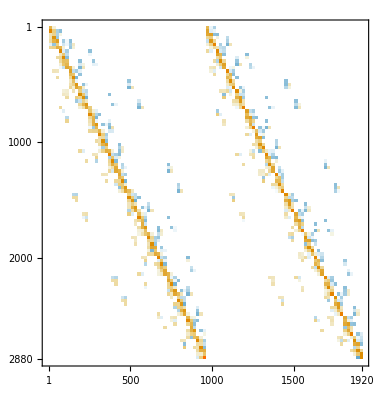

```mathematica
A//MatrixPlot
B//MatrixPlot
```

```mathematica
B+Transpose[CC]//MatrixPlot
```

-Graphics-

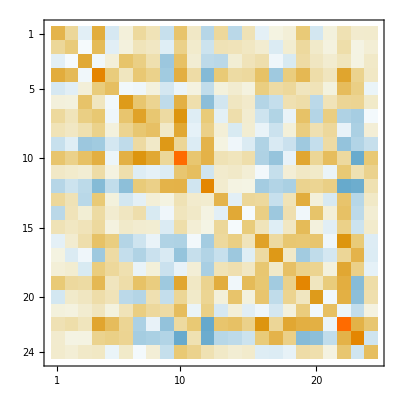

```mathematica
Inverse[Transpose[B].LinearSolve[A,B]]//MatrixPlot
```

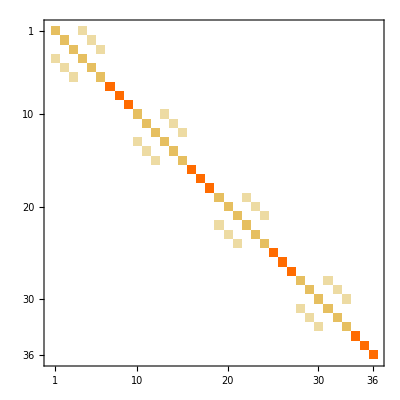

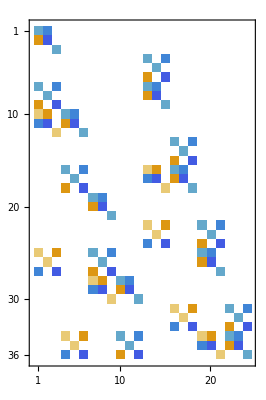

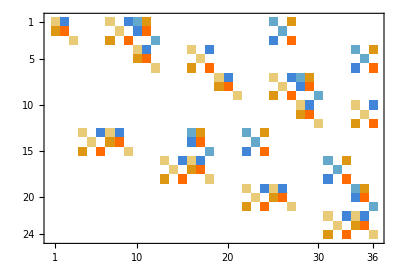

{{1,1}→0.,{1,2}→0.,{2,1}→0.,{2,2}→0.,{3,3}→0.,{4,13}→0.,{4,15}→0.,{5,14}→0.,{6,13}→0.,{6,15}→0.,{7,1}→0.,{7,3}→0.,{7,13}→0.,{7,14}→0.,{8,2}→0.,{8,13}→0.,{8,14}→0.,{9,1}→0.,{9,3}→0.,{9,15}→0.,{10,1}→0.,{10,2}→0.,{10,4}→0.,{10,5}→0.,{11,1}→0.,{11,2}→0.,{11,4}→0.,{11,5}→0.,{12,3}→0.,{12,6}→0.,{13,16}→0.,{13,18}→0.,{14,17}→0.,{15,16}→0.,{15,18}→0.,{16,4}→0.,{16,6}→0.,{16,13}→0.,{16,14}→0.,{16,16}→0.,{16,17}→0.,{17,5}→0.,{17,13}→0.,{17,14}→0.,{17,16}→0.,{17,17}→0.,{18,4}→0.,{18,6}→0.,{18,15}→0.,{18,18}→0.,{19,7}→0.,{19,8}→0.,{20,7}→0.,{20,8}→0.,{21,9}→0.,{22,13}→0.,{22,15}→0.,{22,19}→0.,{22,21}→0.,{23,14}→0.,{23,20}→0.,{24,13}→0.,{24,15}→0.,{24,19}→0.,{24,21}→0.,{25,1}→0.,{25,3}→0.,{25,7}→0.,{25,9}→0.,{25,19}→0.,{25,20}→0.,{26,2}→0.,{26,8}→0.,{26,19}→0.,{26,20}→0.,{27,1}→0.,{27,3}→0.,{27,7}→0.,{27,9}→0.,{27,21}→0.,{28,7}→0.,{28,8}→0.,{28,10}→0.,{28,11}→0.,{29,7}→0.,{29,8}→0.,{29,10}→0.,{29,11}→0.,{30,9}→0.,{30,12}→0.,{31,16}→0.,{31,18}→0.,{31,22}→0.,{31,24}→0.,{32,17}→0.,{32,23}→0.,{33,16}→0.,{33,18}→0.,{33,22}→0.,{33,24}→0.,{34,4}→0.,{34,6}→0.,{34,10}→0.,{34,12}→0.,{34,19}→0.,{34,20}→0.,{34,22}→0.,{34,23}→0.,{35,5}→0.,{35,11}→0.,{35,19}→0.,{35,20}→0.,{35,22}→0.,{35,23}→0.,{36,4}→0.,{36,6}→0.,{36,10}→0.,{36,12}→0.,{36,21}→0.,{36,24}→0.,{_,_}→0}

{}

```mathematica
A//MatrixPlot
B//MatrixPlot
CC//MatrixPlot

B+Transpose[CC]//ArrayRules
```

{{2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,-1.73205,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.73205,-3.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,-1.73205,0,0,0,0,0,0,0,0,0},{0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,0,0,0,0,0,0,0,0,0},{0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.73205,0,-3.,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,-1.73205,0,0,0,0,0,0,0,0,0,-1.,-1.73205,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,0,0,0,0,0,0,0,0,0,1.73205,-3.,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.73205,0,-3.,0,0,0,0,0,0,0,0,0,0,0,-1.,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,1.73205,0,-1.,-1.73205,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.73205,-3.,0,1.73205,-3.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,-1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,-1.73205,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.73205,0,-3.,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,-1.73205,0,0,0,0,0,0,1.,1.73205,0,-1.,-1.73205,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,0,0,0,0,0,0,-1.73205,-3.,0,1.73205,-3.,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.73205,0,-3.,0,0,0,0,0,0,0,0,1.,0,0,-1.,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,-1.73205,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.73205,-3.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,1.73205,0,0,0,-1.,0,-1.73205,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,-1.,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.73205,0,-3.,0,0,0,1.73205,0,-3.,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,0,0,1.,0,1.73205,0,0,0,-1.,0,-1.73205,0,0,0,0,0,0,0,0,0,-1.,-1.73205,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,-1.,0,0,0,0,0,0,0,0,0,0,1.73205,-3.,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,0,0,0,0,0,0,-1.73205,0,-3.,0,0,0,1.73205,0,-3.,0,0,0,0,0,0,0,0,0,0,0,-1.,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,1.,1.73205,0,-1.,-1.73205,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,-1.73205,-3.,0,1.73205,-3.,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,-1.,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,1.73205,0,0,0,-1.,0,-1.73205},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,-1.,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,2.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.73205,0,-3.,0,0,0,1.73205,0,-3.},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,0,0,1.,0,1.73205,0,0,0,-1.,0,-1.73205,0,0,0,0,0,0,1.,1.73205,0,-1.,-1.73205,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,0,0,1.,0,0,0,0,0,-1.,0,0,0,0,0,0,0,-1.73205,-3.,0,1.73205,-3.,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.,0,0,0,-1.73205,0,-3.,0,0,0,1.73205,0,-3.,0,0,0,0,0,0,0,0,1.,0,0,-1.},{-1.,1.73205,0.,0.,0.,0.,-1.,0.,1.73205,1.,-1.73205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,-1.73205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1.73205,-3.,0.,0.,0.,0.,0.,-1.,0.,1.73205,-3.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,-1.,0.,0.,0.,-1.73205,0.,-3.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.73205,0.,-3.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,1.73205,0.,0.,0.,0.,-1.,0.,1.73205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,-1.73205,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.73205,-3.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,-1.73205,0.,-3.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.73205,0.,-3.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,1.73205,0.,0.,0.,0.,-1.,0.,1.73205,1.,-1.73205,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.73205,-3.,0.,0.,0.,0.,0.,-1.,0.,1.73205,-3.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,-1.73205,0.,-3.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,1.73205,0.,0.,0.,0.,-1.,0.,1.73205,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.73205,-3.,0.,0.,0.,0.,0.,-1.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,-1.73205,0.,-3.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,-1.,0.,1.73205,-1.,1.73205,0.,0.,0.,0.,0.,0.,0.,1.,-1.73205,0.,0.,0.,0.,1.,0.,-1.73205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,-1.,0.,-1.73205,-3.,0.,0.,0.,0.,0.,0.,0.,1.73205,-3.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,-1.73205,0.,-3.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.73205,0.,-3.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,1.73205,-1.,1.73205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,-1.73205,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,-1.73205,-3.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.73205,0.,-3.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.73205,0.,-3.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,1.73205,-1.,1.73205,0.,0.,0.,0.,0.,0.,0.,1.,-1.73205,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,-1.73205,-3.,0.,0.,0.,0.,0.,0.,0.,1.73205,-3.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.73205,0.,-3.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,1.73205,-1.,1.73205,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,-1.73205,-3.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.73205,0.,-3.,0.,0.,-1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

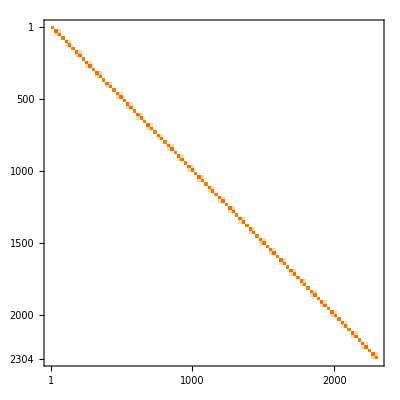

```mathematica
ArrayFlatten[{{A,B},{-CC,0}}]
```

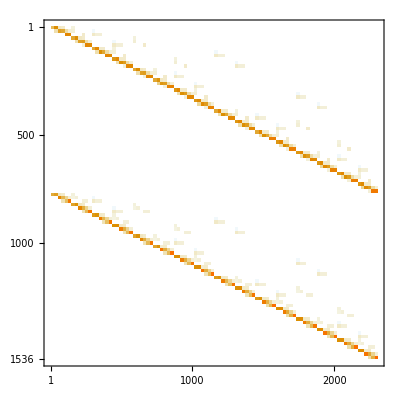

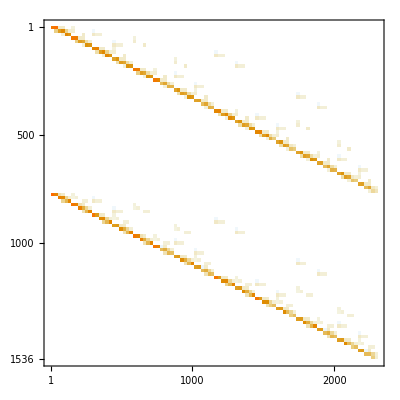

{{1,1}→-0.25,{1,7}→-0.125,{1,9}→0.216506,{2,2}→-0.75,{2,8}→-0.125,{3,3}→-0.25,{3,7}→0.216507,{3,9}→-0.375,{4,10}→-0.125,{4,11}→-0.216506,{4,16}→-0.125,{4,18}→0.216506,{5,10}→-0.216507,{5,11}→-0.375,{5,17}→-0.125,{6,12}→-0.125,{6,16}→0.216507,{6,18}→-0.375,{7,19}→-0.125,{7,20}→0.216506,{7,25}→-0.125,{7,27}→-0.216506,{8,19}→0.216507,{8,20}→-0.375,{8,26}→-0.125,{9,21}→-0.125,{9,25}→-0.216507,{9,27}→-0.375,{13,37}→-0.125,{13,38}→-0.216506,{13,43}→-0.125,{13,45}→0.216506,{14,37}→-0.216507,{14,38}→-0.375,{14,44}→-0.125,{15,39}→-0.125,{15,43}→0.216507,{15,45}→-0.375,{16,46}→-0.125,{16,47}→-0.216506,{16,52}→-0.125,{16,54}→0.216506,{17,46}→-0.216507,{17,47}→-0.375,{17,53}→-0.125,{18,48}→-0.125,{18,52}→0.216507,{18,54}→-0.375,{25,73}→-0.125,{25,74}→0.216506,{25,79}→-0.125,{25,81}→-0.216506,{26,73}→0.216507,{26,74}→-0.375,{26,80}→-0.125,{27,75}→-0.125,{27,79}→-0.216507,{27,81}→-0.375,{31,91}→-0.125,{31,92}→0.216506,{31,97}→-0.125,{31,99}→-0.216506,{32,91}→0.216507,{32,92}→-0.375,{32,98}→-0.125,{33,93}→-0.125,{33,97}→-0.216507,{33,99}→-0.375,{49,145}→-0.125,{49,146}→-0.216506,{49,151}→-0.125,{49,153}→0.216506,{50,145}→-0.216507,{50,146}→-0.375,{50,152}→-0.125,{51,147}→-0.125,{51,151}→0.216507,{51,153}→-0.375,{52,154}→-0.125,{52,155}→-0.216506,{52,160}→-0.125,{52,162}→0.216506,{53,154}→-0.216507,{53,155}→-0.375,{53,161}→-0.125,{54,156}→-0.125,{54,160}→0.216507,{54,162}→-0.375,{61,181}→-0.125,{61,182}→-0.216506,{61,187}→-0.125,{61,189}→0.216506,{62,181}→-0.216507,{62,182}→-0.375,{62,188}→-0.125,{63,183}→-0.125,{63,187}→0.216507,{63,189}→-0.375,{64,190}→-0.125,{64,191}→-0.216506,{64,196}→-0.125,{64,198}→0.216506,{65,190}→-0.216507,{65,191}→-0.375,{65,197}→-0.125,{66,192}→-0.125,{66,196}→0.216507,{66,198}→-0.375,{97,289}→-0.125,{97,290}→0.216506,{97,295}→-0.125,{97,297}→-0.216506,{98,289}→0.216507,{98,290}→-0.375,{98,296}→-0.125,{99,291}→-0.125,{99,295}→-0.216507,{99,297}→-0.375,{103,307}→-0.125,{103,308}→0.216506,{103,313}→-0.125,{103,315}→-0.216506,{104,307}→0.216507,{104,308}→-0.375,{104,314}→-0.125,{105,309}→-0.125,{105,313}→-0.216507,{105,315}→-0.375,{121,361}→-0.125,{121,362}→0.216506,{121,367}→-0.125,{121,369}→-0.216506,{122,361}→0.216507,{122,362}→-0.375,{122,368}→-0.125,{123,363}→-0.125,{123,367}→-0.216507,{123,369}→-0.375,{127,379}→-0.125,{127,380}→0.216506,{127,385}→-0.125,{127,387}→-0.216506,{128,379}→0.216507,{128,380}→-0.375,{128,386}→-0.125,{129,381}→-0.125,{129,385}→-0.216507,{129,387}→-0.375,{193,577}→-0.125,{193,578}→-0.216506,{193,583}→-0.125,{193,585}→0.216506,{194,577}→-0.216507,{194,578}→-0.375,{194,584}→-0.125,{195,579}→-0.125,{195,583}→0.216507,{195,585}→-0.375,{196,586}→-0.125,{196,587}→-0.216506,{196,592}→-0.125,{196,594}→0.216506,{197,586}→-0.216507,{197,587}→-0.375,{197,593}→-0.125,{198,588}→-0.125,{198,592}→0.216507,{198,594}→-0.375,{205,613}→-0.125,{205,614}→-0.216506,{205,619}→-0.125,{205,621}→0.216506,{206,613}→-0.216507,{206,614}→-0.375,{206,620}→-0.125,{207,615}→-0.125,{207,619}→0.216507,{207,621}→-0.375,{208,622}→-0.125,{208,623}→-0.216506,{208,628}→-0.125,{208,630}→0.216506,{209,622}→-0.216507,{209,623}→-0.375,{209,629}→-0.125,{210,624}→-0.125,{210,628}→0.216507,{210,630}→-0.375,{241,721}→-0.125,{241,722}→-0.216506,{241,727}→-0.125,{241,729}→0.216506,{242,721}→-0.216507,{242,722}→-0.375,{242,728}→-0.125,{243,723}→-0.125,{243,727}→0.216507,{243,729}→-0.375,{244,730}→-0.125,{244,731}→-0.216506,{244,736}→-0.125,{244,738}→0.216506,{245,730}→-0.216507,{245,731}→-0.375,{245,737}→-0.125,{246,732}→-0.125,{246,736}→0.216507,{246,738}→-0.375,{253,757}→-0.125,{253,758}→-0.216506,{253,763}→-0.125,{253,765}→0.216506,{254,757}→-0.216507,{254,758}→-0.375,{254,764}→-0.125,{255,759}→-0.125,{255,763}→0.216507,{255,765}→-0.375,{256,766}→0.375,{256,767}→-0.216506,{256,772}→-0.125,{256,774}→0.216506,{257,766}→-0.216506,{257,767}→1.125,{257,773}→-0.125,{258,768}→0.375,{258,772}→0.216507,{258,774}→-0.375,{262,784}→0.25,{263,785}→0.75,{264,786}→0.25,{280,838}→0.25,{281,839}→0.75,{282,840}→0.25,{286,856}→0.25,{287,857}→0.75,{288,858}→0.25,{352,1054}→0.25,{353,1055}→0.75,{354,1056}→0.25,{358,1072}→0.25,{359,1073}→0.75,{360,1074}→0.25,{376,1126}→0.25,{377,1127}→0.75,{378,1128}→0.25,{382,1144}→0.25,{383,1145}→0.75,{384,1146}→0.25,{385,1153}→-0.125,{385,1154}→0.216506,{385,1159}→-0.125,{385,1161}→-0.216506,{386,1153}→0.216507,{386,1154}→-0.375,{386,1160}→-0.125,{387,1155}→-0.125,{387,1159}→-0.216507,{387,1161}→-0.375,{391,1171}→-0.125,{391,1172}→0.216506,{391,1177}→-0.125,{391,1179}→-0.216506,{392,1171}→0.216507,{392,1172}→-0.375,{392,1178}→-0.125,{393,1173}→-0.125,{393,1177}→-0.216507,{393,1179}→-0.375,{409,1225}→-0.125,{409,1226}→0.216506,{409,1231}→-0.125,{409,1233}→-0.216506,{410,1225}→0.216507,{410,1226}→-0.375,{410,1232}→-0.125,{411,1227}→-0.125,{411,1231}→-0.216507,{411,1233}→-0.375,{415,1243}→-0.125,{415,1244}→0.216506,{415,1249}→-0.125,{415,1251}→-0.216506,{416,1243}→0.216507,{416,1244}→-0.375,{416,1250}→-0.125,{417,1245}→-0.125,{417,1249}→-0.216507,{417,1251}→-0.375,{481,1441}→-0.125,{481,1442}→0.216506,{481,1447}→-0.125,{481,1449}→-0.216506,{482,1441}→0.216507,{482,1442}→-0.375,{482,1448}→-0.125,{483,1443}→-0.125,{483,1447}→-0.216507,{483,1449}→-0.375,{487,1459}→-0.125,{487,1460}→0.216506,{487,1465}→-0.125,{487,1467}→-0.216506,{488,1459}→0.216507,{488,1460}→-0.375,{488,1466}→-0.125,{489,1461}→-0.125,{489,1465}→-0.216507,{489,1467}→-0.375,{505,1513}→-0.125,{505,1514}→0.216506,{505,1519}→-0.125,{505,1521}→-0.216506,{506,1513}→0.216507,{506,1514}→-0.375,{506,1520}→-0.125,{507,1515}→-0.125,{507,1519}→-0.216507,{507,1521}→-0.375,{511,1531}→-0.125,{511,1532}→0.216506,{511,1537}→0.125,{511,1539}→-0.216507,{512,1531}→0.216507,{512,1532}→-0.375,{512,1538}→0.125,{513,1533}→-0.125,{513,1537}→-0.216506,{513,1539}→0.375,{514,1546}→0.25,{515,1547}→0.25,{516,1548}→0.75,{523,1573}→0.25,{524,1574}→0.25,{525,1575}→0.75,{526,1582}→0.25,{527,1583}→0.25,{528,1584}→0.75,{559,1681}→0.25,{560,1682}→0.25,{561,1683}→0.75,{562,1690}→0.25,{563,1691}→0.25,{564,1692}→0.75,{571,1717}→0.25,{572,1718}→0.25,{573,1719}→0.75,{574,1726}→0.25,{575,1727}→0.25,{576,1728}→0.75,{640,1918}→0.25,{641,1919}→0.75,{642,1920}→0.25,{646,1936}→0.25,{647,1937}→0.75,{648,1938}→0.25,{664,1990}→0.25,{665,1991}→0.75,{666,1992}→0.25,{670,2008}→0.25,{671,2009}→0.75,{672,2010}→0.25,{703,2113}→0.25,{704,2114}→0.25,{705,2115}→0.75,{706,2122}→0.25,{707,2123}→0.25,{708,2124}→0.75,{715,2149}→0.25,{716,2150}→0.25,{717,2151}→0.75,{718,2158}→0.25,{719,2159}→0.25,{720,2160}→0.75,{736,2206}→0.25,{737,2207}→0.75,{738,2208}→0.25,{742,2224}→0.25,{743,2225}→0.75,{744,2226}→0.25,{751,2257}→0.25,{752,2258}→0.25,{753,2259}→0.75,{754,2266}→0.25,{755,2267}→0.25,{756,2268}→0.75,{760,2278}→0.25,{761,2279}→0.75,{762,2280}→0.25,{763,2293}→0.25,{764,2294}→0.25,{765,2295}→0.75,{766,2296}→0.25,{766,2302}→0.25,{767,2297}→0.75,{767,2303}→0.25,{768,2298}→0.25,{768,2304}→0.75,{769,4}→-0.125,{769,6}→0.216506,{769,7}→-0.25,{770,5}→-0.125,{770,8}→-0.75,{771,4}→0.216507,{771,6}→-0.375,{771,9}→-0.25,{772,13}→-0.125,{772,15}→0.216506,{772,16}→-0.125,{772,17}→-0.216506,{773,14}→-0.125,{773,16}→-0.216507,{773,17}→-0.375,{774,13}→0.216507,{774,15}→-0.375,{774,18}→-0.125,{775,22}→-0.125,{775,24}→-0.216506,{775,25}→-0.125,{775,26}→0.216506,{776,23}→-0.125,{776,25}→0.216507,{776,26}→-0.375,{777,22}→-0.216507,{777,24}→-0.375,{777,27}→-0.125,{781,40}→-0.125,{781,42}→0.216506,{781,43}→-0.125,{781,44}→-0.216506,{782,41}→-0.125,{782,43}→-0.216507,{782,44}→-0.375,{783,40}→0.216507,{783,42}→-0.375,{783,45}→-0.125,{784,49}→-0.125,{784,51}→0.216506,{784,52}→-0.125,{784,53}→-0.216506,{785,50}→-0.125,{785,52}→-0.216507,{785,53}→-0.375,{786,49}→0.216507,{786,51}→-0.375,{786,54}→-0.125,{793,76}→-0.125,{793,78}→-0.216506,{793,79}→-0.125,{793,80}→0.216506,{794,77}→-0.125,{794,79}→0.216507,{794,80}→-0.375,{795,76}→-0.216507,{795,78}→-0.375,{795,81}→-0.125,{799,94}→-0.125,{799,96}→-0.216506,{799,97}→-0.125,{799,98}→0.216506,{800,95}→-0.125,{800,97}→0.216507,{800,98}→-0.375,{801,94}→-0.216507,{801,96}→-0.375,{801,99}→-0.125,{817,148}→-0.125,{817,150}→0.216506,{817,151}→-0.125,{817,152}→-0.216506,{818,149}→-0.125,{818,151}→-0.216507,{818,152}→-0.375,{819,148}→0.216507,{819,150}→-0.375,{819,153}→-0.125,{820,157}→-0.125,{820,159}→0.216506,{820,160}→-0.125,{820,161}→-0.216506,{821,158}→-0.125,{821,160}→-0.216507,{821,161}→-0.375,{822,157}→0.216507,{822,159}→-0.375,{822,162}→-0.125,{829,184}→-0.125,{829,186}→0.216506,{829,187}→-0.125,{829,188}→-0.216506,{830,185}→-0.125,{830,187}→-0.216507,{830,188}→-0.375,{831,184}→0.216507,{831,186}→-0.375,{831,189}→-0.125,{832,193}→-0.125,{832,195}→0.216506,{832,196}→-0.125,{832,197}→-0.216506,{833,194}→-0.125,{833,196}→-0.216507,{833,197}→-0.375,{834,193}→0.216507,{834,195}→-0.375,{834,198}→-0.125,{865,292}→-0.125,{865,294}→-0.216506,{865,295}→-0.125,{865,296}→0.216506,{866,293}→-0.125,{866,295}→0.216507,{866,296}→-0.375,{867,292}→-0.216507,{867,294}→-0.375,{867,297}→-0.125,{871,310}→-0.125,{871,312}→-0.216506,{871,313}→-0.125,{871,314}→0.216506,{872,311}→-0.125,{872,313}→0.216507,{872,314}→-0.375,{873,310}→-0.216507,{873,312}→-0.375,{873,315}→-0.125,{889,364}→-0.125,{889,366}→-0.216506,{889,367}→-0.125,{889,368}→0.216506,{890,365}→-0.125,{890,367}→0.216507,{890,368}→-0.375,{891,364}→-0.216507,{891,366}→-0.375,{891,369}→-0.125,{895,382}→-0.125,{895,384}→-0.216506,{895,385}→-0.125,{895,386}→0.216506,{896,383}→-0.125,{896,385}→0.216507,{896,386}→-0.375,{897,382}→-0.216507,{897,384}→-0.375,{897,387}→-0.125,{961,580}→-0.125,{961,582}→0.216506,{961,583}→-0.125,{961,584}→-0.216506,{962,581}→-0.125,{962,583}→-0.216507,{962,584}→-0.375,{963,580}→0.216507,{963,582}→-0.375,{963,585}→-0.125,{964,589}→-0.125,{964,591}→0.216506,{964,592}→-0.125,{964,593}→-0.216506,{965,590}→-0.125,{965,592}→-0.216507,{965,593}→-0.375,{966,589}→0.216507,{966,591}→-0.375,{966,594}→-0.125,{973,616}→-0.125,{973,618}→0.216506,{973,619}→-0.125,{973,620}→-0.216506,{974,617}→-0.125,{974,619}→-0.216507,{974,620}→-0.375,{975,616}→0.216507,{975,618}→-0.375,{975,621}→-0.125,{976,625}→-0.125,{976,627}→0.216506,{976,628}→-0.125,{976,629}→-0.216506,{977,626}→-0.125,{977,628}→-0.216507,{977,629}→-0.375,{978,625}→0.216507,{978,627}→-0.375,{978,630}→-0.125,{1009,724}→-0.125,{1009,726}→0.216506,{1009,727}→-0.125,{1009,728}→-0.216506,{1010,725}→-0.125,{1010,727}→-0.216507,{1010,728}→-0.375,{1011,724}→0.216507,{1011,726}→-0.375,{1011,729}→-0.125,{1012,733}→-0.125,{1012,735}→0.216506,{1012,736}→-0.125,{1012,737}→-0.216506,{1013,734}→-0.125,{1013,736}→-0.216507,{1013,737}→-0.375,{1014,733}→0.216507,{1014,735}→-0.375,{1014,738}→-0.125,{1021,760}→-0.125,{1021,762}→0.216506,{1021,763}→-0.125,{1021,764}→-0.216506,{1022,761}→-0.125,{1022,763}→-0.216507,{1022,764}→-0.375,{1023,760}→0.216507,{1023,762}→-0.375,{1023,765}→-0.125,{1024,769}→-0.125,{1024,771}→0.216506,{1024,772}→0.375,{1024,773}→-0.216506,{1025,770}→-0.125,{1025,772}→-0.216506,{1025,773}→1.125,{1026,769}→0.216507,{1026,771}→-0.375,{1026,774}→0.375,{1030,790}→0.25,{1031,791}→0.75,{1032,792}→0.25,{1048,844}→0.25,{1049,845}→0.75,{1050,846}→0.25,{1054,862}→0.25,{1055,863}→0.75,{1056,864}→0.25,{1120,1060}→0.25,{1121,1061}→0.75,{1122,1062}→0.25,{1126,1078}→0.25,{1127,1079}→0.75,{1128,1080}→0.25,{1144,1132}→0.25,{1145,1133}→0.75,{1146,1134}→0.25,{1150,1150}→0.25,{1151,1151}→0.75,{1152,1152}→0.25,{1153,1156}→-0.125,{1153,1158}→-0.216506,{1153,1159}→-0.125,{1153,1160}→0.216506,{1154,1157}→-0.125,{1154,1159}→0.216507,{1154,1160}→-0.375,{1155,1156}→-0.216507,{1155,1158}→-0.375,{1155,1161}→-0.125,{1159,1174}→-0.125,{1159,1176}→-0.216506,{1159,1177}→-0.125,{1159,1178}→0.216506,{1160,1175}→-0.125,{1160,1177}→0.216507,{1160,1178}→-0.375,{1161,1174}→-0.216507,{1161,1176}→-0.375,{1161,1179}→-0.125,{1177,1228}→-0.125,{1177,1230}→-0.216506,{1177,1231}→-0.125,{1177,1232}→0.216506,{1178,1229}→-0.125,{1178,1231}→0.216507,{1178,1232}→-0.375,{1179,1228}→-0.216507,{1179,1230}→-0.375,{1179,1233}→-0.125,{1183,1246}→-0.125,{1183,1248}→-0.216506,{1183,1249}→-0.125,{1183,1250}→0.216506,{1184,1247}→-0.125,{1184,1249}→0.216507,{1184,1250}→-0.375,{1185,1246}→-0.216507,{1185,1248}→-0.375,{1185,1251}→-0.125,{1249,1444}→-0.125,{1249,1446}→-0.216506,{1249,1447}→-0.125,{1249,1448}→0.216506,{1250,1445}→-0.125,{1250,1447}→0.216507,{1250,1448}→-0.375,{1251,1444}→-0.216507,{1251,1446}→-0.375,{1251,1449}→-0.125,{1255,1462}→-0.125,{1255,1464}→-0.216506,{1255,1465}→-0.125,{1255,1466}→0.216506,{1256,1463}→-0.125,{1256,1465}→0.216507,{1256,1466}→-0.375,{1257,1462}→-0.216507,{1257,1464}→-0.375,{1257,1467}→-0.125,{1273,1516}→-0.125,{1273,1518}→-0.216506,{1273,1519}→-0.125,{1273,1520}→0.216506,{1274,1517}→-0.125,{1274,1519}→0.216507,{1274,1520}→-0.375,{1275,1516}→-0.216507,{1275,1518}→-0.375,{1275,1521}→-0.125,{1279,1534}→0.125,{1279,1536}→-0.216507,{1279,1537}→-0.125,{1279,1538}→0.216506,{1280,1535}→0.125,{1280,1537}→0.216507,{1280,1538}→-0.375,{1281,1534}→-0.216506,{1281,1536}→0.375,{1281,1539}→-0.125,{1282,1543}→0.25,{1283,1544}→0.25,{1284,1545}→0.75,{1291,1570}→0.25,{1292,1571}→0.25,{1293,1572}→0.75,{1294,1579}→0.25,{1295,1580}→0.25,{1296,1581}→0.75,{1327,1678}→0.25,{1328,1679}→0.25,{1329,1680}→0.75,{1330,1687}→0.25,{1331,1688}→0.25,{1332,1689}→0.75,{1339,1714}→0.25,{1340,1715}→0.25,{1341,1716}→0.75,{1342,1723}→0.25,{1343,1724}→0.25,{1344,1725}→0.75,{1408,1924}→0.25,{1409,1925}→0.75,{1410,1926}→0.25,{1414,1942}→0.25,{1415,1943}→0.75,{1416,1944}→0.25,{1432,1996}→0.25,{1433,1997}→0.75,{1434,1998}→0.25,{1438,2014}→0.25,{1439,2015}→0.75,{1440,2016}→0.25,{1471,2110}→0.25,{1472,2111}→0.25,{1473,2112}→0.75,{1474,2119}→0.25,{1475,2120}→0.25,{1476,2121}→0.75,{1483,2146}→0.25,{1484,2147}→0.25,{1485,2148}→0.75,{1486,2155}→0.25,{1487,2156}→0.25,{1488,2157}→0.75,{1504,2212}→0.25,{1505,2213}→0.75,{1506,2214}→0.25,{1510,2230}→0.25,{1511,2231}→0.75,{1512,2232}→0.25,{1519,2254}→0.25,{1520,2255}→0.25,{1521,2256}→0.75,{1522,2263}→0.25,{1523,2264}→0.25,{1524,2265}→0.75,{1528,2284}→0.25,{1529,2285}→0.75,{1530,2286}→0.25,{1531,2290}→0.25,{1532,2291}→0.25,{1533,2292}→0.75,{1534,2299}→0.25,{1534,2302}→0.25,{1535,2300}→0.25,{1535,2303}→0.75,{1536,2301}→0.75,{1536,2304}→0.25,{_,_}→0}

```mathematica
CC//MatrixPlot
-Transpose[B]//MatrixPlot
CC+Transpose[B]//Normal//Chop//SparseArray//ArrayRules
```

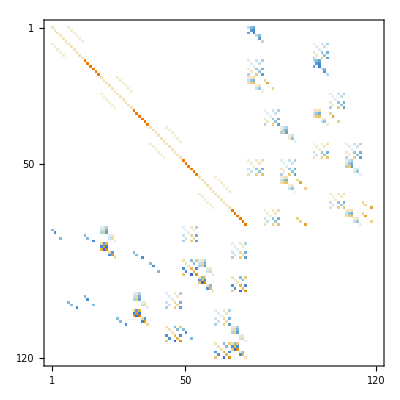

```mathematica
Chop[Normal[AA]]//MatrixPlot
```

```mathematica
AA//ArrayRules
```

{{1,1}→0.142222,{1,2}→0.0711111,{1,3}→-0.0355556,{1,4}→0.0711111,{1,5}→0.0355556,{1,6}→-0.0177778,{1,7}→-0.0355556,{1,8}→-0.0177778,{1,9}→0.00888889,{1,10}→0.0711111,{1,11}→0.0355556,{1,12}→-0.0177778,{1,13}→0.0355556,{1,14}→0.0177778,{1,15}→-0.00888889,{1,16}→-0.0177778,{1,17}→-0.00888889,{1,18}→0.00444444,{2,2}→0.568889,{2,1}→0.0711111,{2,3}→0.0711111,{2,4}→0.0355556,{2,5}→0.284444,{2,6}→0.0355556,{2,7}→-0.0177778,{2,8}→-0.142222,{2,9}→-0.0177778,{2,10}→0.0355556,{2,11}→0.284444,{2,12}→0.0355556,{2,13}→0.0177778,{2,14}→0.142222,{2,15}→0.0177778,{2,16}→-0.00888889,{2,17}→-0.0711111,{2,18}→-0.00888889,{3,3}→0.142222,{3,1}→-0.0355556,{3,2}→0.0711111,{3,4}→-0.0177778,{3,5}→0.0355556,{3,6}→0.0711111,{3,7}→0.00888889,{3,8}→-0.0177778,{3,9}→-0.0355556,{3,10}→-0.0177778,{3,11}→0.0355556,{3,12}→0.0711111,{3,13}→-0.00888889,{3,14}→0.0177778,{3,15}→0.0355556,{3,16}→0.00444444,{3,17}→-0.00888889,{3,18}→-0.0177778,{4,4}→0.568889,{4,1}→0.0711111,{4,2}→0.0355556,{4,3}→-0.0177778,{4,5}→0.284444,{4,6}→-0.142222,{4,7}→0.0711111,{4,8}→0.0355556,{4,9}→-0.0177778,{4,10}→0.0355556,{4,11}→0.0177778,{4,12}→-0.00888889,{4,13}→0.284444,{4,14}→0.142222,{4,15}→-0.0711111,{4,16}→0.0355556,{4,17}→0.0177778,{4,18}→-0.00888889,{5,5}→2.27556,{5,1}→0.0355556,{5,2}→0.284444,{5,3}→0.0355556,{5,4}→0.284444,{5,6}→0.284444,{5,7}→0.0355556,{5,8}→0.284444,{5,9}→0.0355556,{5,10}→0.0177778,{5,11}→0.142222,{5,12}→0.0177778,{5,13}→0.142222,{5,14}→1.13778,{5,15}→0.142222,{5,16}→0.0177778,{5,17}→0.142222,{5,18}→0.0177778,{6,6}→0.568889,{6,1}→-0.0177778,{6,2}→0.0355556,{6,3}→0.0711111,{6,4}→-0.142222,{6,5}→0.284444,{6,7}→-0.0177778,{6,8}→0.0355556,{6,9}→0.0711111,{6,10}→-0.00888889,{6,11}→0.0177778,{6,12}→0.0355556,{6,13}→-0.0711111,{6,14}→0.142222,{6,15}→0.284444,{6,16}→-0.00888889,{6,17}→0.0177778,{6,18}→0.0355556,{7,7}→0.142222,{7,1}→-0.0355556,{7,2}→-0.0177778,{7,3}→0.00888889,{7,4}→0.0711111,{7,5}→0.0355556,{7,6}→-0.0177778,{7,8}→0.0711111,{7,9}→-0.0355556,{7,10}→-0.0177778,{7,11}→-0.00888889,{7,12}→0.00444444,{7,13}→0.0355556,{7,14}→0.0177778,{7,15}→-0.00888889,{7,16}→0.0711111,{7,17}→0.0355556,{7,18}→-0.0177778,{8,8}→0.568889,{8,1}→-0.0177778,{8,2}→-0.142222,{8,3}→-0.0177778,{8,4}→0.0355556,{8,5}→0.284444,{8,6}→0.0355556,{8,7}→0.0711111,{8,9}→0.0711111,{8,10}→-0.00888889,{8,11}→-0.0711111,{8,12}→-0.00888889,{8,13}→0.0177778,{8,14}→0.142222,{8,15}→0.0177778,{8,16}→0.0355556,{8,17}→0.284444,{8,18}→0.0355556,{9,9}→0.142222,{9,1}→0.00888889,{9,2}→-0.0177778,{9,3}→-0.0355556,{9,4}→-0.0177778,{9,5}→0.0355556,{9,6}→0.0711111,{9,7}→-0.0355556,{9,8}→0.0711111,{9,10}→0.00444444,{9,11}→-0.00888889,{9,12}→-0.0177778,{9,13}→-0.00888889,{9,14}→0.0177778,{9,15}→0.0355556,{9,16}→-0.0177778,{9,17}→0.0355556,{9,18}→0.0711111,{10,10}→0.142222,{10,1}→0.0711111,{10,2}→0.0355556,{10,3}→-0.0177778,{10,4}→0.0355556,{10,5}→0.0177778,{10,6}→-0.00888889,{10,7}→-0.0177778,{10,8}→-0.00888889,{10,9}→0.00444444,{10,11}→0.0711111,{10,12}→-0.0355556,{10,13}→0.0711111,{10,14}→0.0355556,{10,15}→-0.0177778,{10,16}→-0.0355556,{10,17}→-0.0177778,{10,18}→0.00888889,{11,11}→0.568889,{11,1}→0.0355556,{11,2}→0.284444,{11,3}→0.0355556,{11,4}→0.0177778,{11,5}→0.142222,{11,6}→0.0177778,{11,7}→-0.00888889,{11,8}→-0.0711111,{11,9}→-0.00888889,{11,10}→0.0711111,{11,12}→0.0711111,{11,13}→0.0355556,{11,14}→0.284444,{11,15}→0.0355556,{11,16}→-0.0177778,{11,17}→-0.142222,{11,18}→-0.0177778,{12,12}→0.142222,{12,1}→-0.0177778,{12,2}→0.0355556,{12,3}→0.0711111,{12,4}→-0.00888889,{12,5}→0.0177778,{12,6}→0.0355556,{12,7}→0.00444444,{12,8}→-0.00888889,{12,9}→-0.0177778,{12,10}→-0.0355556,{12,11}→0.0711111,{12,13}→-0.0177778,{12,14}→0.0355556,{12,15}→0.0711111,{12,16}→0.00888889,{12,17}→-0.0177778,{12,18}→-0.0355556,{13,13}→0.568889,{13,1}→0.0355556,{13,2}→0.0177778,{13,3}→-0.00888889,{13,4}→0.284444,{13,5}→0.142222,{13,6}→-0.0711111,{13,7}→0.0355556,{13,8}→0.0177778,{13,9}→-0.00888889,{13,10}→0.0711111,{13,11}→0.0355556,{13,12}→-0.0177778,{13,14}→0.284444,{13,15}→-0.142222,{13,16}→0.0711111,{13,17}→0.0355556,{13,18}→-0.0177778,{14,14}→2.27556,{14,1}→0.0177778,{14,2}→0.142222,{14,3}→0.0177778,{14,4}→0.142222,{14,5}→1.13778,{14,6}→0.142222,{14,7}→0.0177778,{14,8}→0.142222,{14,9}→0.0177778,{14,10}→0.0355556,{14,11}→0.284444,{14,12}→0.0355556,{14,13}→0.284444,{14,15}→0.284444,{14,16}→0.0355556,{14,17}→0.284444,{14,18}→0.0355556,{15,15}→0.568889,{15,1}→-0.00888889,{15,2}→0.0177778,{15,3}→0.0355556,{15,4}→-0.0711111,{15,5}→0.142222,{15,6}→0.284444,{15,7}→-0.00888889,{15,8}→0.0177778,{15,9}→0.0355556,{15,10}→-0.0177778,{15,11}→0.0355556,{15,12}→0.0711111,{15,13}→-0.142222,{15,14}→0.284444,{15,16}→-0.0177778,{15,17}→0.0355556,{15,18}→0.0711111,{16,16}→0.142222,{16,1}→-0.0177778,{16,2}→-0.00888889,{16,3}→0.00444444,{16,4}→0.0355556,{16,5}→0.0177778,{16,6}→-0.00888889,{16,7}→0.0711111,{16,8}→0.0355556,{16,9}→-0.0177778,{16,10}→-0.0355556,{16,11}→-0.0177778,{16,12}→0.00888889,{16,13}→0.0711111,{16,14}→0.0355556,{16,15}→-0.0177778,{16,17}→0.0711111,{16,18}→-0.0355556,{17,17}→0.568889,{17,1}→-0.00888889,{17,2}→-0.0711111,{17,3}→-0.00888889,{17,4}→0.0177778,{17,5}→0.142222,{17,6}→0.0177778,{17,7}→0.0355556,{17,8}→0.284444,{17,9}→0.0355556,{17,10}→-0.0177778,{17,11}→-0.142222,{17,12}→-0.0177778,{17,13}→0.0355556,{17,14}→0.284444,{17,15}→0.0355556,{17,16}→0.0711111,{17,18}→0.0711111,{18,18}→0.142222,{18,1}→0.00444444,{18,2}→-0.00888889,{18,3}→-0.0177778,{18,4}→-0.00888889,{18,5}→0.0177778,{18,6}→0.0355556,{18,7}→-0.0177778,{18,8}→0.0355556,{18,9}→0.0711111,{18,10}→0.00888889,{18,11}→-0.0177778,{18,12}→-0.0355556,{18,13}→-0.0177778,{18,14}→0.0355556,{18,15}→0.0711111,{18,16}→-0.0355556,{18,17}→0.0711111,{19,19}→1.13778,{19,20}→0.568889,{19,21}→-0.284444,{19,22}→0.568889,{19,23}→0.284444,{19,24}→-0.142222,{19,25}→-0.284444,{19,26}→-0.142222,{19,27}→0.0711111,{20,20}→4.55111,{20,19}→0.568889,{20,21}→0.568889,{20,22}→0.284444,{20,23}→2.27556,{20,24}→0.284444,{20,25}→-0.142222,{20,26}→-1.13778,{20,27}→-0.142222,{21,21}→1.13778,{21,19}→-0.284444,{21,20}→0.568889,{21,22}→-0.142222,{21,23}→0.284444,{21,24}→0.568889,{21,25}→0.0711111,{21,26}→-0.142222,{21,27}→-0.284444,{22,22}→4.55111,{22,19}→0.568889,{22,20}→0.284444,{22,21}→-0.142222,{22,23}→2.27556,{22,24}→-1.13778,{22,25}→0.568889,{22,26}→0.284444,{22,27}→-0.142222,{23,23}→18.2044,{23,19}→0.284444,{23,20}→2.27556,{23,21}→0.284444,{23,22}→2.27556,{23,24}→2.27556,{23,25}→0.284444,{23,26}→2.27556,{23,27}→0.284444,{24,24}→4.55111,{24,19}→-0.142222,{24,20}→0.284444,{24,21}→0.568889,{24,22}→-1.13778,{24,23}→2.27556,{24,25}→-0.142222,{24,26}→0.284444,{24,27}→0.568889,{25,25}→1.13778,{25,19}→-0.284444,{25,20}→-0.142222,{25,21}→0.0711111,{25,22}→0.568889,{25,23}→0.284444,{25,24}→-0.142222,{25,26}→0.568889,{25,27}→-0.284444,{26,26}→4.55111,{26,19}→-0.142222,{26,20}→-1.13778,{26,21}→-0.142222,{26,22}→0.284444,{26,23}→2.27556,{26,24}→0.284444,{26,25}→0.568889,{26,27}→0.568889,{27,27}→1.13778,{27,19}→0.0711111,{27,20}→-0.142222,{27,21}→-0.284444,{27,22}→-0.142222,{27,23}→0.284444,{27,24}→0.568889,{27,25}→-0.284444,{27,26}→0.568889,{_,_}→0}

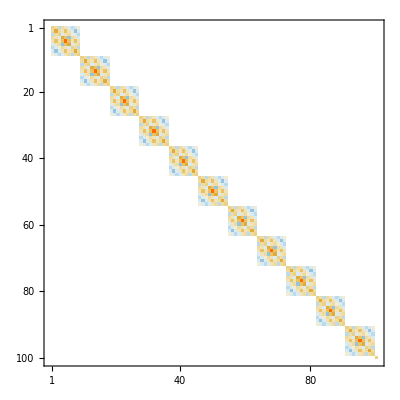

```mathematica
b
```